# Kalman Folding versus Particle Filtering

Brian Beckman
16 Mar 2018

## Abstract

Kalman Folding is equivalent to Renormalized Recurrent Least Squares, and is Bayesian by construction (Beckman, 2018, https://goo.gl/CwLYjf). Therefore, it regularizes well. Sticking with concrete, numerical examples, we show that particle filtering can approximate the results of Kalman Folding. For a more theoretical analysis, see Fernández-Villaverde (http://www.ssc.upenn.edu/~jesusfv/filters_format.pdf).

## Bishop’s Example

Chris Bishop’s Pattern Recognition and Machine Learning has an extended example fitting higher-order polynomials, linear in their coefficients, to non-linear data, starting in section 1.1.

Bishop’s Training Set

First, a function to produce a sequence of Ν inputs for a training set, equally spaced in [0..1].

```mathematica
ClearAll[bishopTrainingSetX];
bishopTrainingSetX[Ν_]:=Array[Identity,Ν,{0.,1.}];
```

Bishop’s ground truth is a single cycle of a sine wave. Add noise to a sample taken at the inputs of the training set above. Bishop doesn’t state an observation noise, but I guess σ_z (my notation)=σ_t (Bishop's Notation)=0.30 to create a fake data set that resembles Bishop’s qualitatively.

Wolfram’s built-in NormalDistribution takes the standard deviation as its second argument, not the variance. Mixing up standard deviation and variance is an easy mistake. Bishop’s notation for normal distribution takes variance as second argument, so beware.

```mathematica
ClearAll[bishopTrainingSetY,bishopGroundTruthY];
bishopGroundTruthY[xs_]:=Sin[2.π#]&/@xs;
bishopTrainingSetY[xs_,σ_]:=
With[{n=Length@xs},
bishopGroundTruthY[xs]
+RandomVariate[NormalDistribution[0.,σ],n]];
```

Take a sample of the outputs and assign it the names bts for bishopTrainingSet.

```mathematica
ClearAll[bishopTrainingSet,bts,bishopFake,bishopFakeSigma];
bishopFake[n_,σ_]:=
With[{xs=bishopTrainingSetX[n]},
With[{ys=bishopTrainingSetY[xs,σ]},
{xs,ys}]];
bishopFakeSigma=0.30;
bishopTrainingSet=bts=bishopFake[10,bishopFakeSigma];
```

Make a plot like Bishop’s figure 1.7 (page 10).

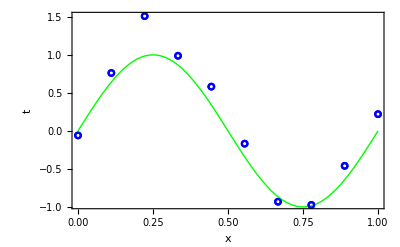

```mathematica
With[{lp=ListPlot[btsᵀ,
PlotMarkers->{Graphics@{Blue,Circle[{0,0},1]},.05}]},
Show[{lp,(* once to set the scale *)
Plot[Sin[2.π x],{x,0.,1.},PlotStyle->{Thick,Green}],
lp (* again to overdraw the continuous plot *)},
Frame->True,
FrameLabel->{"x","t"}]]
```

Partials: Gradients of the Unknown Parameters

Write a function for partials (features).

Produces a Ν×(Μ+1) matrix: one row for each datum, one column for each term in the fitting polynomial:

#### partialsFn [ order, xs : sequence-of-inputs ]

```mathematica
ClearAll[partialsFn];
partialsFn[order_,xs_]:=
Transpose@Quiet@Table[#^(i-1)/.{Indeterminate->1},{i,order+1}]&@xs;
```

A convenience function:

#### symbolicPowers [ variable, order ]

```mathematica
ClearAll[symbolicPowers];
symbolicPowers[variable_,order_]:=
partialsFn[order,{variable}]⟦1⟧;
```

## Renormalized Recurrent Least Squares (RRLS)

(equivalent to a Kalman filter, just with slightly better numerics):

```mathematica
ClearAll[rlsUpdate];
rlsUpdate[sqrtPΖ_][{ξ_,Λ_},{ζ_,a_}]:=
With[{sPΖia=LinearSolve[sqrtPΖ,a]},
With[{Π=(Λ+sPΖiaᵀ.sPΖia)},
{LinearSolve[Π,(sPΖiaᵀ.ζ+Λ.ξ)],Π}]];
```

Given observation variance σ_ζ^2 and a-priori variance σ_ξ^2 for the vector ξ of coefficients, a polynomial order Μ, and a training set as a list of parallel arrays of length Ν, construct an a-priori estimate ξ_0 for the coefficients

```mathematica
ClearAll[rrlsFit];
rrlsFit[σ2ζ_,σ2ξ_][Μ_,trainingSet_]:=
With[{xs=trainingSet⟦1⟧,ys=trainingSet⟦2⟧},
With[{ξ0=List/@ConstantArray[0,Μ+1],
Λ0=σ2ξ^-1*IdentityMatrix[Μ+1]},
Module[{ξ,Λ},
{ξ,Λ}=Fold[
rlsUpdate[√σ2ζ IdentityMatrix[1]],(* assumes scalar 1×1 observations ζ *)
{ξ0,Λ0},
{List/@ys,List/@partialsFn[Μ,xs]}ᵀ];
{ξ/√σ2ζ,Λ}]]];
```

Explore RRLS on Bishop’s example:

```mathematica
Manipulate[Module[{x},
With[{σζ2=10.^(2logσζ),σξ2=10.^(2logσξ)},
With[{rrls=Quiet@rrlsFit[σζ2,σξ2][Μ,bts]},
<|"σζ2"->σζ2,"σξ2"-> σξ2,"rrls⟦1⟧"->MatrixForm[goodSolution=rrls⟦1⟧]|>
]]],
Column[{
Button["RESET",(Μ=9;logσξ=.5;logσζ=-1.5)&],
Control[{{Μ,9,"order Μ"},0,16,1,Appearance->{"Labeled"}}],Control[{{logσξ,.5,"log σξ (KAL)"},-3, 5,Appearance->"Labeled"}],
Control[{{logσζ,-1.5,"log σζ (KAL)"},-7,3,Appearance->"Labeled"}]}]]
```

#### goodSolution

Save a good solution for later comparison against the particle filter:

```mathematica
Dynamic[goodSolution]
```

a graphical exploration:

```mathematica
Manipulate[Module[{x},
With[{
terms=symbolicPowers[x,Μ],
cs=ϕ[Μ]/@List/@bts⟦1⟧,
ts=bts⟦2⟧,
σζ2=10.^(2logσζ),σξ2=10.^(2logσξ)},
With[{rrls=Quiet@rrlsFit[σζ2,σξ2][Μ,bts]},
With[{rrlsFn={terms}.rrls⟦1⟧},
With[{lp=ListPlot[btsᵀ,
PlotMarkers->{Graphics@{Blue,Circle[{0,0},1]},.05}]},
Module[{showlist={lp,Plot[Sin[2.π x],{x,0.,1.},PlotStyle->{Thick,Green}]}},
AppendTo[showlist,Plot[rrlsFn,{x,0,1},PlotStyle->{Purple}]];Quiet@Show[showlist,Frame->True,ImageSize->Medium,FrameLabel->{{"ζ",""},{"ξ",Grid[{{"α: ",α,"β:",β}}]
}}]]]]]]],
Column[{
Button["RESET",(Μ=4;logσξ=.5;logσζ=-1.5)&],
Control[{{Μ,4,"order Μ"},0,16,1,Appearance->{"Labeled"}}],Control[{{logσξ,.5,"log σξ"},-3, 5,Appearance->"Labeled"}],
Control[{{logσζ,-1.5,"log σζ"},-7,3,Appearance->"Labeled"}]}]]
```

## Particle Filter

Each particle ξ^i,i∈[1.. N_s], is an (Μ+1)-vector guess at the state, i.e., the column vector of coefficients. There are N_s of them for each time tick in the simulation.

Initialization

```mathematica
ClearAll[P,P0,ξ0,ξ0s,importanceFunctions];
ClearAll[Ns,σ0,σ,ξ,ξs,Μ,Ν,ws];

Ns=500; (* number of particles (samples) *)

Μ=9; (* order of the polynomial *)
Ν=10; (* number of data to fit *)
p=0.10; (* fraction of particles to save each round *)

σ0=10; (* initial standard deviation for generating particles *)

(* column vector: one copy of σ0 for each component of a particle *)
σ[0]=List/@ConstantArray[σ0,Μ+1]; 

(* column vector: initial particles *)
ξ[0]=List/@ConstantArray[0.,Μ+1]; 

(* (Μ+1)×Subscript[N, s] particles in a matrix *)
ξs[0]=
Table[
ξ[0]⟦i,1⟧+RandomVariate[NormalDistribution[ξ[0]⟦i,1⟧,σ[0]⟦i,1⟧]],
{i,Μ+1},{j,Ns}];

(* initial weights *)
ws[0]=ConstantArray[1./Ns,Ns];

Print[<|"sum of weights"->Plus@@ws[0],"Dimensions@ξ[0]"->Dimensions@ξ[0],"Dimensions[ξs[0]]"->Dimensions[ξs[0]]|>]
```

<|sum of weights→1.,Dimensions@ξ[0]→{10,1},Dimensions[ξs[0]]→{10,500}|>

3D Point Clouds

Explore the initial particles, which are 10-dimensional in the running example, three dimensions at a time.

```mathematica
ClearAll[threeDPointClouds];
threeDPointClouds[ξs_,σ_]:=
DynamicModule[{i=1,j=2,k=3},
Manipulate[Graphics3D[Point/@({ξs⟦i,All⟧,ξs⟦j,All⟧,ξs⟦k,All⟧}ᵀ),
Axes->True,AspectRatio->1,
AxesLabel->{"i: "<>ToString[i],"j: "<>ToString[j],"k: "<>ToString[k]},PlotRange->3{{-σ,σ},{-σ,σ},{-σ,σ}}],
Grid[{
{"i",SetterBar[Dynamic[i],Range[Μ+1]]},
{"j",SetterBar[Dynamic[j],Range[Μ+1]]},
{"k",SetterBar[Dynamic[k],Range[Μ+1]]}}]]];
threeDPointClouds[ξs[0],σ0]
```

Observations and Residuals

Observations are constant with time in the running example, but we include a time parameter for generality. The particle cloud changes with time due to resampling.

When Mathematica slices a matrix with the ⟦All,n⟧ operation, it produces a one-dimensional list. For some purposes, a one-dimensional list can stand in for a column vector, which is a two-dimensional matrix with one column. However, a one-dimensional list cannot be transposed, so it is actually improper. Mapping List over a one-dimensional list is a standard way to convert it into a proper column vector.

```mathematica
ClearAll[ξcol];
ξcol[t_,n_/;(1≤n≤Ns)]:=List/@ξs[t]⟦All,n⟧;
```

```mathematica
ClearAll[ζcol];
ζcol[t_]:=List/@bts⟦2⟧
```

#### scalar [ singleton-matrix-or-list ]

By preferring proper column and row vectors, we often get 1×1 matrices and lists, and we need a way to fetch the scalars inside such things.

```mathematica
ClearAll[scalar];
scalar[{{m_}}/;(Head@m=!=List)]:=m;
scalar[{m_}/;(Head@m=!=List)]:=m;
scalar[x___]:=Throw["improper input type for 'scalar': "<>ToString[m]];
```

#### conjColumns [ matrix-1, matrix-2 ]

We need a way to conjoin columns:

```mathematica
ClearAll[conjColumns];
conjColumns[m1_,m2_]:=((m1ᵀ)~Join~(m2ᵀ))ᵀ;
```

#### residuals [ time, particle-number ]

Mean and StandardDeviation are documented as column-wise over matrices. so they are ideal for computing residuals, i.e., differences between modeled outputs (labels) and actual data:

(-24.0129 | 4.83113 | 2.11939 | 10.3623 | 10.78 | -8.37968 | 6.48477 | -6.48077 | 4.90364 | -14.1431 | -1.37966 | -11.8408 | 4.49189 | -3.57141 | 5.01413 | -11.273 | -8.40447 | 15.7585 | 3.81091 | -2.82748 | 7.4129 | -1.00008 | -5.14142 | -2.68097 | 4.52762 | 2.08859 | -16.2321 | -1.1504 | -6.69271 | -4.0992 | 28.9656 | -7.1019 | -30.0693 | -5.46912 | 7.30816 | 3.81817 | -2.02764 | 14.3389 | 7.40395 | 11.6188 | 16.906 | 5.34086 | -2.58152 | -1.83656 | 17.3139 | -1.11275 | 0.136065 | -19.426 | -3.49114 | 19.6627 | -7.84981 | -6.35012 | 7.71323 | -7.89957 | -7.70607 | 0.0207613 | -7.07153 | 2.76879 | 13.2318 | -3.01945 | 0.868204 | -0.387431 | 2.91912 | 8.00616 | 0.413688 | 3.222 | 8.59666 | -8.54894 | 4.77977 | -2.52486 | 22.1979 | 10.0569 | -3.96292 | -4.36132 | 11.5858 | -4.73321 | -0.387353 | 4.55583 | -9.95648 | 0.269417 | 23.3228 | 1.45536 | 2.60471 | 15.2964 | -4.12234 | 11.6664 | -1.07213 | 25.1141 | 24.5941 | 4.90259 | -0.938943 | -7.59335 | -11.9216 | 19.6216 | 9.05369 | -9.18771 | -0.186579 | 2.76751 | 7.15457 | 16.474 | 8.45556 | 1.59651 | -8.41732 | -6.02065 | -4.67053 | -5.2519 | 22.3562 | -10.9937 | -1.93388 | -14.8483 | 16.1152 | 7.41238 | -4.40965 | 16.1484 | 0.430652 | -18.5721 | 0.126817 | 0.0267838 | -17.3028 | 1.39334 | -5.37517 | -6.99106 | 11.0485 | -12.1585 | -11.6561 | 0.943233 | 6.02021 | 1.02273 | -20.3335 | 0.536372 | 1.51415 | 6.74289 | 0.22697 | 2.31729 | -0.050718 | -20.945 | 2.04283 | -1.67856 | -4.46215 | -0.0668468 | -20.471 | -3.48143 | 18.3835 | 17.6124 | -24.5978 | -0.319925 | 3.24178 | 2.91999 | 5.6367 | -3.41264 | -3.46359 | 0.569028 | -11.0183 | 1.98067 | -3.74344 | 10.2356 | 24.0394 | 5.61972 | 18.0959 | -13.6916 | 8.17671 | -16.3459 | -13.3778 | 3.24822 | 3.52224 | 12.0462 | -4.27173 | -1.72155 | -1.28588 | 0.618328 | 12.7228 | 3.80723 | 19.9169 | 9.61646 | 5.17996 | -4.80201 | -9.52712 | 6.55389 | 0.96698 | -16.9367 | -25.1519 | 21.9899 | 10.781 | -12.2851 | -3.27182 | -20.1044 | 10.6546 | 4.98101 | 2.97715 | 3.90149 | -8.9029 | 29.6407 | -1.4001 | -12.2893 | -2.14726 | 9.42506 | -4.87182 | 0.767981 | -3.18492 | -25.4896 | -2.67404 | 3.94231 | 0.00565174 | 8.79098 | -6.55142 | -1.2334 | 3.36515 | 3.09973 | -4.49751 | 0.527944 | -9.50376 | 1.82788 | -2.94771 | 10.9303 | 8.8871 | -8.89438 | -1.7564 | 1.91903 | 10.1532 | 11.561 | 6.50971 | -8.65377 | 2.74806 | 16.6055 | -14.7589 | 3.0081 | 2.68507 | -5.60654 | 8.64202 | 1.04298 | 19.294 | 9.84907 | -5.691 | 7.37294 | -4.88025 | 6.12904 | 1.93333 | 9.21142 | 9.92556 | 3.77424 | -15.673 | -6.92032 | -12.0758 | -3.73178 | -4.9956 | -0.29171 | 4.85065 | 4.41514 | 8.79041 | -7.87779 | -0.814435 | 5.95621 | 5.12207 | -13.7636 | 7.5386 | -17.9022 | 7.49682 | -1.87083 | 19.2229 | -6.61769 | -9.82823 | -2.62859 | -10.2854 | -19.3759 | 6.04136 | -17.0964 | -4.08242 | -1.47388 | -4.07802 | -14.1274 | -15.413 | 22.9108 | 9.54651 | 21.1983 | 4.44589 | -1.83912 | -5.54966 | -0.714922 | -3.05336 | -12.3933 | -19.2714 | 9.50824 | 6.82201 | 5.95322 | -7.232 | -0.676199 | 6.23484 | 13.226 | -8.95153 | 2.50736 | -17.6338 | 2.76063 | 4.54038 | -11.6774 | 1.86647 | -14.3345 | -11.7268 | -7.94079 | 19.5273 | 6.61305 | 1.42561 | 6.96417 | 1.70536 | 9.99646 | 5.77538 | -16.7836 | 0.948042 | -3.45653 | -3.11143 | -13.0614 | 18.9418 | -1.07709 | 5.4727 | -1.74759 | 19.2071 | -6.02804 | 4.45486 | -6.97937 | -2.78791 | 3.62815 | 11.003 | -5.39025 | -7.97141 | -8.54565 | -5.05477 | -1.85693 | 8.21094 | 5.38002 | -9.14986 | 0.468599 | 17.8841 | -4.46787 | 0.960458 | 4.47504 | -18.0202 | -3.57685 | -14.3712 | 3.18128 | -12.1881 | -6.37139 | -2.78349 | -9.77743 | 17.8022 | -11.5671 | -4.1761 | 0.525554 | -0.115133 | -3.30241 | -1.71184 | 0.351034 | -15.129 | 5.8549 | -1.97059 | 15.8253 | -13.8647 | -1.65386 | 5.51701 | 8.69356 | -7.70126 | 15.6726 | -17.2026 | -5.34493 | 1.43935 | 11.4507 | 3.06831 | -6.12662 | -18.331 | -10.973 | 9.19755 | -9.6882 | -2.46298 | -7.97945 | -2.52441 | -6.44649 | -2.68469 | 3.00879 | -3.99569 | 20.2477 | 3.93781 | -10.101 | -11.1902 | -19.3236 | -4.99643 | -6.82975 | -1.0132 | -14.3045 | 3.92428 | -6.94792 | -10.5763 | -10.9743 | 7.45435 | 2.46393 | -0.78308 | -0.0935454 | 3.55162 | -15.4436 | 0.716313 | 7.50103 | 1.23033 | 10.4102 | 3.81955 | 2.43926 | -14.6045 | -19.6743 | 2.4997 | 6.10524 | 6.15235 | -13.543 | 3.18614 | -1.26896 | 3.16299 | -8.31327 | -12.7722 | 16.7751 | 3.58918 | -11.2186 | -10.675 | 5.39996 | -6.94566 | -12.1446 | -14.0751 | 5.10479 | -14.2825 | 17.1608 | 4.95273 | 0.0885447 | 12.0443 | 6.07906 | -5.55919 | -7.01838 | -7.53413 | -15.4828 | 10.7833 | -7.84602 | 8.16798 | -9.08795 | -7.09093 | 5.9658 | 5.36618 | 4.93862 | 11.3359 | -12.6533 | 5.9001 | 7.59206 | 7.50131 | 6.16891 | 3.28941 | 5.14747 | 4.27776 | -0.581275 | 8.76712 | 10.7927 | -1.77336 | -11.707 | -12.3416 | -1.75204 | -6.69377 | -0.709423 | -2.9304 | -19.8775 | 7.20808 | 15.2629 | -2.75826 | 4.19357 | 3.35483 | 0.284024 | 0.66565 | 9.11826 | -0.776664 | 14.7697 | 2.62383 | -7.75099 | -1.21111 | 10.9245 | 2.87925 | -18.3277 | 18.5753 | 19.2766 | -1.2646 | 4.0297 | 3.7823 | 8.34168 | -14.7511 | -4.18968 | 1.31214 | 9.55488 | -16.2579 | -15.7643 | 5.05347 | -6.29246 | -4.1747 | 11.2338 | -0.456693 | -22.3741 | 7.04734 | -15.6286 | 9.73966 | -6.36487 | 6.28572 | 15.2324
-25.6213 | 2.40967 | 0.628215 | 9.36274 | 9.38349 | -8.65256 | 7.92807 | -7.86691 | 4.36136 | -14.6361 | -2.38917 | -10.5182 | 3.76193 | -2.95996 | 5.97075 | -12.7482 | -10.1262 | 14.8279 | 2.89298 | -4.2771 | 7.87096 | -2.22518 | -5.70253 | -2.79993 | 3.2245 | 1.1801 | -15.9265 | -1.96197 | -8.00107 | -5.13302 | 28.6314 | -8.00375 | -32.1469 | -5.06833 | 6.77214 | 1.37296 | -1.86305 | 13.9702 | 5.83334 | 9.62404 | 17.0145 | 3.77918 | -2.40294 | -1.38624 | 13.7519 | -1.35379 | -0.856202 | -20.9325 | -3.63812 | 18.5571 | -7.8153 | -7.97057 | 6.16358 | -8.89424 | -7.54556 | -0.0500044 | -7.09483 | 1.84637 | 13.4764 | -3.61242 | 0.302987 | 0.188301 | 1.69396 | 7.81217 | 1.53908 | 1.72694 | 7.69764 | -9.19208 | 3.27168 | -3.30825 | 19.2471 | 10.8725 | -5.67418 | -5.23858 | 10.2926 | -5.81238 | -2.04298 | 2.90917 | -9.17356 | 0.886475 | 22.3761 | 0.921459 | 2.8073 | 14.4508 | -3.56428 | 11.5418 | -0.967563 | 22.447 | 23.4422 | 2.94097 | -3.07242 | -5.5576 | -13.7084 | 18.3619 | 7.50081 | -9.85863 | -0.944376 | 0.665982 | 7.96588 | 16.6404 | 7.45521 | 0.339855 | -6.9925 | -7.38077 | -4.31647 | -5.98368 | 22.1805 | -10.2994 | -3.80163 | -17.0156 | 14.5393 | 7.157 | -3.65881 | 13.9076 | -0.043735 | -20.1408 | 1.69385 | 1.14087 | -18.8272 | 0.0847919 | -5.53581 | -7.16818 | 9.55566 | -12.9937 | -14.3922 | -0.129938 | 3.24058 | 0.903508 | -21.2257 | -0.841935 | 0.609326 | 5.94259 | -2.07416 | 0.0495543 | -0.56798 | -23.3302 | 3.13006 | -1.42121 | -5.29736 | 0.940577 | -21.529 | -2.36119 | 18.2774 | 16.6159 | -24.9639 | -1.61706 | 1.12887 | 3.12814 | 5.17803 | -2.15384 | -5.08485 | -2.36262 | -11.5399 | 0.800259 | -5.02585 | 10.4945 | 23.9639 | 5.56909 | 16.3959 | -16.3322 | 6.73531 | -17.1709 | -14.3057 | 3.3688 | 2.22281 | 10.1142 | -5.52694 | -2.76409 | -0.432644 | -0.489405 | 13.2676 | 2.20736 | 17.9036 | 9.21304 | 4.67505 | -5.53506 | -11.7974 | 5.23962 | -0.279317 | -18.4804 | -25.999 | 22.288 | 9.05371 | -13.2136 | -3.75669 | -22.0851 | 9.69196 | 2.54826 | 3.18432 | 3.88054 | -10.685 | 30.2182 | -0.785118 | -13.965 | -1.42675 | 7.42505 | -5.36015 | 1.58599 | -5.05601 | -26.5363 | -3.51571 | 4.54933 | 0.589139 | 6.97161 | -7.92645 | -3.60605 | 3.02163 | 1.35593 | -4.37649 | 0.725898 | -11.5684 | 0.145302 | -1.1966 | 10.0267 | 8.36706 | -11.4157 | -2.39342 | 1.64451 | 12.4306 | 11.1579 | 5.57982 | -10.3268 | 1.46057 | 16.1752 | -14.3294 | 1.71941 | 3.85401 | -7.23788 | 7.24012 | 1.94269 | 19.0462 | 8.80903 | -6.50014 | 6.99882 | -6.01997 | 2.82858 | -0.692934 | 8.64859 | 9.26535 | 2.19255 | -16.8833 | -8.91888 | -12.772 | -5.17819 | -4.07544 | -0.292026 | 5.1574 | 2.22474 | 7.43015 | -10.0981 | -1.38583 | 4.72918 | 4.36032 | -14.7345 | 6.8294 | -19.1274 | 5.04275 | -2.84724 | 17.0604 | -7.38341 | -9.84664 | -1.46896 | -12.313 | -18.8983 | 4.31251 | -19.1924 | -5.5567 | -1.58935 | -4.71944 | -16.1281 | -13.8492 | 20.4089 | 8.636 | 20.9985 | 2.96441 | -2.58633 | -5.09934 | -1.08382 | -4.70588 | -13.0395 | -19.812 | 7.12513 | 5.16981 | 5.01026 | -7.69049 | -3.25022 | 4.89045 | 13.6328 | -8.44453 | 2.95096 | -19.9273 | 4.36683 | 3.90886 | -13.2727 | 1.03995 | -18.6374 | -12.8495 | -8.43366 | 20.7135 | 5.83097 | -0.48333 | 6.6058 | 1.05018 | 9.93401 | 5.99575 | -18.5864 | -2.42267 | -3.09914 | -2.46934 | -13.1143 | 17.789 | -2.13953 | 6.21916 | -1.90754 | 17.2113 | -6.50623 | 3.89699 | -8.57618 | -4.68407 | 2.37036 | 11.0868 | -6.48153 | -9.31171 | -9.66018 | -4.79393 | -2.6427 | 6.41957 | 3.92297 | -10.6599 | 0.668476 | 18.7587 | -3.66326 | 0.611316 | 2.55987 | -18.0525 | -4.84929 | -16.0422 | 3.80366 | -12.9385 | -6.00001 | -5.11256 | -10.4965 | 17.2717 | -12.5823 | -4.32173 | 0.0747575 | -1.20693 | -3.16672 | -1.93399 | -0.135213 | -15.3746 | 4.83245 | -3.4124 | 15.9822 | -14.8198 | -2.65927 | 5.56434 | 8.55264 | -7.75324 | 14.5392 | -19.0917 | -5.09757 | -0.729086 | 11.4175 | 2.53778 | -6.87134 | -18.1632 | -12.3559 | 8.36556 | -9.70375 | -4.13341 | -8.80748 | -3.30294 | -7.31214 | -3.59379 | 1.15001 | -4.0672 | 18.2977 | 3.98838 | -11.8721 | -11.779 | -20.4931 | -6.16645 | -8.3272 | -1.77314 | -15.4399 | 4.44842 | -7.29345 | -12.3148 | -11.9424 | 8.37908 | 1.31666 | -2.11456 | -2.35765 | 3.7608 | -15.4677 | -1.55409 | 6.75766 | 0.602981 | 10.3456 | 2.94422 | 1.85243 | -16.0905 | -20.848 | 1.13603 | 5.94418 | 5.63381 | -14.4045 | 3.07152 | -0.912637 | 0.118209 | -8.59875 | -13.1294 | 15.2229 | 2.73586 | -12.8152 | -12.6992 | 4.00453 | -8.81092 | -12.1237 | -12.4294 | 3.42778 | -13.2007 | 13.5561 | 3.51393 | -1.18847 | 12.5968 | 4.888 | -6.23356 | -8.04595 | -8.75773 | -15.1977 | 10.1075 | -7.96398 | 7.65036 | -11.3786 | -7.44953 | 5.14779 | 5.51304 | 4.36223 | 11.9376 | -14.6907 | 3.22421 | 8.05165 | 6.40764 | 7.34883 | 1.72325 | 2.83145 | 3.71289 | -0.305181 | 8.72277 | 8.70175 | -2.96242 | -11.7539 | -14.7355 | -3.55655 | -8.19405 | -4.02397 | -3.46249 | -20.87 | 6.93774 | 14.5129 | -3.65715 | 2.11377 | 6.08432 | -0.156368 | 0.432897 | 9.35197 | -3.89852 | 15.0085 | 2.44931 | -7.70484 | -1.66792 | 7.72782 | 3.19295 | -17.8632 | 18.3235 | 18.2394 | -0.844397 | 3.55845 | 3.70213 | 7.31002 | -15.0275 | -4.12408 | -0.184144 | 9.71611 | -17.3856 | -17.78 | 5.39545 | -6.14156 | -4.8533 | 9.09569 | -0.616815 | -23.7182 | 6.92274 | -17.9295 | 10.1055 | -7.7771 | 5.46721 | 14.2244
-26.9288 | -0.325909 | -1.0352 | 8.88105 | 7.98677 | -8.5831 | 9.56606 | -8.92251 | 4.01622 | -14.9118 | -3.26937 | -9.03383 | 3.18767 | -2.20599 | 6.9165 | -14.2711 | -11.7644 | 13.5125 | 2.18449 | -5.62999 | 8.2603 | -3.26501 | -6.21718 | -2.67563 | 2.18353 | 0.439296 | -15.5007 | -2.81999 | -9.1295 | -5.93838 | 28.4574 | -8.69988 | -34.0193 | -5.05353 | 5.94163 | -0.91594 | -1.42614 | 13.9412 | 4.56052 | 7.91804 | 17.2245 | 1.91661 | -2.26529 | -0.588075 | 10.1489 | -1.50195 | -1.72183 | -22.3746 | -3.62782 | 17.7793 | -7.39451 | -8.97049 | 5.09695 | -9.70478 | -7.69843 | 0.0163417 | -6.84963 | 1.30457 | 13.7782 | -3.92397 | -0.396801 | 0.571886 | 0.558547 | 7.46726 | 2.37667 | 0.488147 | 6.66016 | -9.81785 | 1.85156 | -3.79764 | 16.767 | 11.7389 | -7.5769 | -6.4836 | 8.93703 | -6.72783 | -3.90784 | 1.39438 | -8.50278 | 1.92515 | 21.6818 | 0.60572 | 3.3232 | 13.6098 | -2.86146 | 11.5034 | -0.535672 | 19.5119 | 22.5902 | 1.16533 | -5.06301 | -3.21979 | -15.0086 | 16.6689 | 6.08624 | -10.3903 | -1.90773 | -1.34002 | 8.36266 | 17.1681 | 5.82303 | -1.34329 | -5.20914 | -8.59743 | -3.7937 | -6.2202 | 22.0599 | -9.52176 | -6.19508 | -19.1847 | 12.8201 | 6.68207 | -2.86208 | 11.708 | -0.183832 | -21.7569 | 3.56161 | 2.35756 | -20.1311 | -0.634395 | -5.20457 | -6.8551 | 8.25308 | -13.4014 | -17.1477 | -1.16609 | 0.222419 | 0.709243 | -21.9783 | -2.00921 | -0.413055 | 5.12759 | -4.63322 | -1.99472 | -1.39449 | -25.7987 | 4.14902 | -1.27246 | -6.08984 | 2.15119 | -22.2799 | -1.46956 | 18.0203 | 15.8532 | -25.123 | -2.85006 | -1.27042 | 3.5281 | 4.55912 | -0.989427 | -6.58837 | -5.67133 | -12.1318 | -0.268837 | -6.43536 | 11.0408 | 24.133 | 5.47974 | 14.1097 | -19.2495 | 5.53652 | -18.0919 | -14.9881 | 3.34013 | 0.750873 | 8.12534 | -6.202 | -3.98251 | 0.711333 | -1.30965 | 13.5182 | 0.296541 | 16.2487 | 8.84553 | 4.16258 | -5.98184 | -13.9677 | 4.0594 | -1.45209 | -20.1678 | -26.6987 | 22.6625 | 7.08125 | -14.1508 | -4.10086 | -23.9778 | 8.75417 | 0.295195 | 3.53588 | 4.01068 | -12.6997 | 30.7373 | 0.281872 | -15.6538 | -0.133692 | 5.49189 | -5.75187 | 2.51984 | -6.71405 | -27.2931 | -4.18617 | 4.94957 | 1.49027 | 5.29878 | -9.31625 | -5.55286 | 3.02353 | 0.0602867 | -3.96303 | 0.914973 | -13.5727 | -1.23418 | 0.840368 | 9.28266 | 7.72826 | -14.1876 | -2.62311 | 1.59454 | 14.9092 | 11.2087 | 4.65614 | -12.0609 | 0.526814 | 16.0331 | -13.4241 | 0.0710366 | 4.71131 | -8.74854 | 5.69641 | 2.47726 | 19.259 | 8.2392 | -7.19874 | 6.94717 | -7.55642 | -0.62267 | -3.31486 | 7.99948 | 8.30136 | 0.74637 | -17.4862 | -10.5945 | -13.3408 | -6.95791 | -2.61442 | -0.218872 | 5.49919 | 0.599208 | 5.88711 | -12.2881 | -2.1587 | 3.47075 | 3.55128 | -15.9531 | 6.42281 | -20.0521 | 2.29205 | -4.21099 | 15.0185 | -8.456 | -9.67156 | 0.192962 | -14.7563 | -18.2097 | 2.891 | -21.0946 | -6.45082 | -1.25562 | -5.16137 | -18.1489 | -12.5361 | 17.743 | 7.70096 | 20.8664 | 1.51372 | -3.7566 | -4.42177 | -1.28687 | -6.14654 | -13.0398 | -20.3683 | 5.05501 | 3.42673 | 3.51449 | -8.18691 | -5.59845 | 3.43991 | 14.3119 | -7.99498 | 3.24877 | -22.1627 | 6.08893 | 3.58372 | -14.7429 | 0.0575946 | -23.4205 | -13.9617 | -8.91796 | 21.8718 | 5.05942 | -2.07929 | 6.5 | 0.500734 | 9.77899 | 6.55838 | -20.014 | -6.09803 | -2.78349 | -2.0258 | -12.7524 | 16.7718 | -2.99078 | 6.86622 | -2.07307 | 15.0958 | -6.6833 | 3.51578 | -10.2696 | -7.18165 | 1.27699 | 11.5845 | -7.74937 | -10.8738 | -11.0164 | -4.38999 | -3.39375 | 4.6619 | 2.7055 | -12.0952 | 1.10394 | 19.9073 | -2.51898 | 0.869778 | 0.161676 | -17.9694 | -6.48794 | -17.5123 | 4.47693 | -13.6438 | -5.31113 | -7.45878 | -10.5595 | 16.6708 | -13.1806 | -4.20618 | -0.292509 | -2.18597 | -2.95457 | -2.29714 | -1.00412 | -15.7017 | 3.86936 | -4.74529 | 16.2595 | -15.5968 | -3.64189 | 5.93629 | 8.20921 | -7.6413 | 13.5526 | -21.3173 | -4.78414 | -2.95858 | 11.2422 | 2.0045 | -7.72871 | -17.8305 | -13.732 | 7.74715 | -9.82299 | -6.12805 | -9.27903 | -4.06437 | -8.07955 | -4.88747 | -0.75882 | -4.78804 | 16.6537 | 4.4075 | -13.5498 | -11.9673 | -20.9901 | -7.44586 | -9.66843 | -2.52436 | -16.7782 | 4.97083 | -7.55808 | -13.825 | -12.9115 | 9.09258 | 0.286553 | -3.29215 | -4.0633 | 3.60146 | -15.2907 | -3.91036 | 5.80027 | 0.0378765 | 10.0781 | 1.93407 | 1.07073 | -17.8369 | -22.0447 | -0.567955 | 5.97327 | 5.76881 | -15.141 | 3.19762 | -0.473449 | -2.91464 | -8.86358 | -13.3055 | 13.5993 | 2.18743 | -14.6345 | -14.8831 | 2.86066 | -10.3835 | -11.8804 | -10.7556 | 1.53693 | -11.5406 | 9.83337 | 2.19697 | -2.62017 | 13.2795 | 3.9875 | -7.28107 | -9.06043 | -9.83358 | -14.8683 | 9.575 | -7.97756 | 6.8887 | -13.6819 | -8.19711 | 4.78087 | 5.37714 | 4.15411 | 12.3349 | -16.6805 | 1.08198 | 8.28691 | 5.34046 | 8.47047 | -0.359878 | 0.689505 | 3.76271 | -0.21488 | 8.45192 | 6.65432 | -3.92521 | -11.609 | -17.0956 | -5.28981 | -9.45225 | -7.21624 | -4.09143 | -21.7104 | 6.62843 | 14.2805 | -4.41426 | -0.169535 | 8.82272 | -0.349646 | 0.319617 | 9.79978 | -7.37236 | 15.3845 | 2.62561 | -7.17923 | -2.15549 | 4.58226 | 3.52826 | -17.2498 | 17.9642 | 16.9617 | -0.21772 | 3.48539 | 3.80567 | 6.10831 | -14.704 | -4.03011 | -1.88743 | 9.9387 | -18.6321 | -19.4159 | 5.31814 | -5.26689 | -5.58304 | 7.4453 | -0.600984 | -24.8181 | 7.21794 | -19.9421 | 10.5977 | -9.53518 | 4.79147 | 13.7716
-26.6126 | -2.39066 | -1.54773 | 10.2117 | 7.74444 | -6.85709 | 12.5737 | -8.2251 | 5.17797 | -13.785 | -2.54055 | -6.12083 | 4.06361 | -0.0989984 | 8.94295 | -14.7037 | -12.1785 | 12.9924 | 2.83332 | -5.59238 | 9.70144 | -3.07286 | -5.65361 | -0.999523 | 2.58241 | 1.03927 | -13.75 | -2.45901 | -8.90502 | -5.33727 | 29.5822 | -8.05612 | -34.4004 | -4.28772 | 6.02778 | -1.90187 | 0.643816 | 15.5618 | 4.95744 | 7.80411 | 18.6491 | 1.05131 | -0.992252 | 1.82827 | 7.52937 | -0.419017 | -1.12334 | -22.3969 | -2.26402 | 18.5777 | -5.28788 | -8.06711 | 5.8249 | -9.03619 | -7.11561 | 1.38205 | -4.94961 | 2.38573 | 15.2728 | -2.61391 | -0.321486 | 1.77633 | 0.840526 | 8.24478 | 3.91529 | 0.675016 | 6.59869 | -9.18958 | 1.79202 | -2.73453 | 16.0882 | 13.8134 | -8.4261 | -7.02835 | 8.70192 | -6.40765 | -4.89739 | 0.941038 | -6.82102 | 4.687 | 22.362 | 1.5869 | 5.4395 | 13.94 | -0.71689 | 12.7147 | 1.56724 | 17.3848 | 23.1059 | 0.631105 | -5.64424 | 0.668136 | -14.5604 | 15.7749 | 5.98873 | -9.61727 | -1.98335 | -2.10679 | 9.3167 | 19.1229 | 4.58749 | -2.20137 | -1.82364 | -8.55012 | -1.86873 | -4.74497 | 23.1855 | -7.50755 | -8.11481 | -20.1848 | 12.1472 | 7.26107 | -0.706649 | 10.7886 | 1.26662 | -22.142 | 6.80856 | 4.84963 | -20.1378 | 0.46833 | -3.17991 | -4.65927 | 8.37352 | -12.1617 | -18.6523 | -1.06406 | -1.75694 | 1.63058 | -21.4988 | -1.84126 | -0.356661 | 5.45239 | -6.42124 | -2.55625 | -1.31771 | -27.3585 | 6.31245 | -0.158536 | -5.67421 | 4.74526 | -21.2747 | 0.287113 | 18.6998 | 16.4417 | -23.8405 | -2.9682 | -2.79782 | 5.36709 | 4.88712 | 1.07285 | -6.70799 | -8.07053 | -11.6372 | 0.223474 | -6.67688 | 13.2403 | 25.7075 | 6.60594 | 12.2574 | -21.365 | 5.84236 | -17.9857 | -14.1168 | 4.35004 | 0.335342 | 7.29302 | -4.97169 | -4.28251 | 3.3851 | -0.528835 | 14.7345 | -0.72057 | 16.1039 | 9.61692 | 4.90498 | -4.92285 | -14.8745 | 4.22774 | -1.33222 | -20.7652 | -26.1886 | 24.5163 | 6.11635 | -13.9347 | -3.1401 | -24.3518 | 8.87114 | -0.587558 | 5.38439 | 5.48647 | -13.9489 | 32.4166 | 2.91092 | -16.1532 | 3.12401 | 4.7575 | -4.68768 | 4.74322 | -6.95995 | -26.3975 | -3.35092 | 6.51154 | 3.90632 | 4.87506 | -9.5561 | -5.84846 | 4.63803 | 0.483407 | -1.99018 | 2.44432 | -14.252 | -0.998504 | 4.47282 | 9.83152 | 8.22235 | -16.06 | -1.18797 | 3.02511 | 18.6543 | 13.0716 | 5.1056 | -12.4846 | 1.20574 | 17.416 | -10.8106 | -0.976271 | 6.62963 | -8.92644 | 5.34912 | 3.86378 | 21.223 | 9.32635 | -6.59938 | 8.49706 | -8.25316 | -3.01681 | -4.54294 | 8.61347 | 8.34664 | 0.942656 | -16.1145 | -10.6882 | -12.5668 | -7.87341 | 0.625789 | 1.0484 | 7.22179 | 0.913567 | 5.40139 | -13.2649 | -1.90741 | 3.35122 | 3.86718 | -16.3028 | 7.56159 | -19.3365 | 0.445846 | -4.91196 | 14.2031 | -8.69907 | -8.10029 | 3.46967 | -16.6186 | -16.1923 | 2.82686 | -21.5627 | -5.40628 | 0.799328 | -4.24437 | -19.1937 | -10.3336 | 15.9225 | 7.90729 | 22.0359 | 1.38831 | -4.20032 | -2.14756 | -0.0592758 | -6.1311 | -10.9882 | -19.7755 | 4.68707 | 2.79192 | 2.44412 | -7.65447 | -6.36482 | 3.17906 | 16.5393 | -6.33561 | 4.73126 | -23.1197 | 9.06725 | 4.68367 | -14.8599 | -0.00550604 | -27.561 | -13.8304 | -8.08209 | 24.3562 | 5.44392 | -2.12304 | 7.76356 | 1.3037 | 10.7601 | 8.71104 | -19.9333 | -9.00013 | -1.32825 | -0.565273 | -10.7507 | 17.0002 | -2.417 | 8.45487 | -1.21732 | 13.9632 | -5.4371 | 4.44296 | -10.7479 | -9.20117 | 1.61324 | 13.645 | -8.00498 | -11.4575 | -11.3597 | -2.65173 | -2.92915 | 4.07051 | 2.99279 | -12.2956 | 2.80136 | 22.442 | 0.111459 | 3.13944 | -1.59367 | -16.5233 | -7.32415 | -17.6909 | 6.27276 | -13.2786 | -3.07157 | -8.53418 | -8.69223 | 17.186 | -12.267 | -2.45946 | 0.466017 | -1.94266 | -1.29632 | -1.60397 | -1.18629 | -14.7635 | 3.99887 | -4.57657 | 17.8417 | -15.1103 | -3.48553 | 7.81542 | 8.69778 | -6.16709 | 13.8573 | -22.7936 | -3.33071 | -3.97706 | 12.1274 | 2.69777 | -7.45242 | -16.336 | -13.8423 | 8.68699 | -8.7286 | -7.5661 | -8.28239 | -3.55013 | -7.4812 | -5.33691 | -1.62199 | -5.06111 | 16.4758 | 6.51817 | -13.7499 | -10.6463 | -19.4054 | -7.69707 | -9.62244 | -2.01375 | -17.0992 | 6.64379 | -6.59832 | -13.8888 | -12.6603 | 10.7225 | 0.646493 | -3.34617 | -3.85625 | 4.27362 | -13.5158 | -5.28058 | 5.86161 | 0.504403 | 10.615 | 1.79461 | 1.24194 | -18.718 | -22.1975 | -1.43782 | 7.44213 | 7.79537 | -14.588 | 4.62892 | 1.40134 | -4.85609 | -7.85677 | -11.9535 | 13.1037 | 3.18253 | -15.7584 | -16.1515 | 2.94036 | -10.4455 | -10.2174 | -7.66216 | 0.646893 | -7.91706 | 7.37867 | 2.1286 | -3.21734 | 15.4772 | 4.61559 | -7.54166 | -8.96076 | -9.4226 | -13.2952 | 10.224 | -6.72207 | 6.83201 | -14.782 | -8.12211 | 6.14017 | 6.16358 | 5.49823 | 13.6162 | -17.5685 | 0.641825 | 9.37985 | 5.57186 | 10.7287 | -1.71181 | -0.195373 | 5.92318 | 1.06173 | 9.01368 | 6.04404 | -3.25074 | -9.92321 | -18.22 | -5.80669 | -9.18424 | -9.11759 | -3.59509 | -21.0909 | 7.45252 | 15.9363 | -3.83337 | -1.41865 | 12.8693 | 0.901896 | 1.52826 | 11.6825 | -9.99587 | 17.134 | 4.39221 | -4.94873 | -1.57761 | 2.70439 | 5.20996 | -15.2564 | 18.7927 | 16.6321 | 1.85503 | 4.88938 | 5.40271 | 5.90198 | -12.6248 | -2.69952 | -2.69516 | 11.2195 | -19.0181 | -19.4449 | 5.92811 | -2.34715 | -5.28553 | 7.38012 | 0.791741 | -24.4477 | 9.2155 | -20.4693 | 12.4514 | -10.526 | 5.60083 | 15.1012
-25.9191 | -5.37456 | -2.17176 | 12.0595 | 7.11234 | -4.70026 | 15.4687 | -6.80655 | 6.57242 | -12.6847 | -1.27175 | -3.02942 | 5.15117 | 2.04851 | 10.5252 | -15.5273 | -12.8423 | 11.7904 | 3.44125 | -5.34662 | 10.7512 | -3.25686 | -5.58872 | 1.06033 | 2.90361 | 1.55898 | -11.9646 | -2.15887 | -8.77116 | -4.77495 | 30.5905 | -7.63694 | -34.5663 | -4.12268 | 5.66412 | -2.96904 | 3.04643 | 17.6456 | 5.79056 | 8.06754 | 19.8666 | -0.0135835 | -0.042074 | 4.57947 | 4.30888 | 0.311217 | -0.186991 | -22.1953 | -0.944859 | 19.6375 | -2.73146 | -6.58436 | 7.14468 | -8.13185 | -7.34456 | 2.65378 | -2.47124 | 3.78766 | 16.437 | -0.943934 | -1.15996 | 2.2363 | 1.34964 | 8.88136 | 4.55709 | 0.836068 | 6.06643 | -8.59765 | 1.8923 | -1.41915 | 15.9004 | 15.6092 | -9.55745 | -8.4098 | 8.25683 | -6.43454 | -6.5765 | -0.234527 | -5.5262 | 7.99331 | 22.8659 | 2.30078 | 7.89168 | 14.0457 | 1.63352 | 13.8451 | 4.17185 | 14.5228 | 23.4399 | -0.158515 | -6.18157 | 4.68732 | -13.6312 | 14.4645 | 5.7755 | -9.02268 | -2.73194 | -3.04524 | 9.14288 | 20.9842 | 2.18045 | -3.54463 | 1.75212 | -8.66204 | 0.100654 | -2.94994 | 24.1012 | -5.72204 | -11.2825 | -21.4372 | 11.0495 | 7.65229 | 1.49585 | 9.70523 | 3.06037 | -22.5218 | 9.9126 | 7.32196 | -20.4283 | 2.09063 | -0.756454 | -1.73061 | 8.55561 | -10.6393 | -20.1487 | -1.30842 | -3.99676 | 2.31435 | -21.3058 | -1.78848 | -0.54898 | 5.46304 | -8.98712 | -2.9491 | -1.59689 | -29.6821 | 8.25826 | 0.408112 | -5.47868 | 7.30408 | -19.5501 | 1.38837 | 18.7918 | 16.9471 | -22.4787 | -3.56354 | -5.02912 | 7.3654 | 4.75753 | 2.37458 | -6.85991 | -10.8139 | -11.5412 | 1.16565 | -7.04827 | 15.8994 | 27.2483 | 7.62232 | 9.20812 | -24.3533 | 6.35816 | -18.356 | -13.026 | 5.01325 | -0.322055 | 6.2155 | -3.0665 | -5.06874 | 6.31707 | 0.577214 | 15.6936 | -2.16941 | 15.9912 | 9.93623 | 5.63274 | -3.80223 | -15.938 | 4.46651 | -1.2816 | -21.4633 | -25.9729 | 26.6987 | 4.77754 | -14.1001 | -2.3439 | -24.2278 | 8.45568 | -1.48707 | 7.56528 | 6.90203 | -15.9738 | 33.8756 | 5.57268 | -16.8921 | 7.2363 | 3.68467 | -3.34314 | 6.86377 | -7.17954 | -25.0674 | -2.23628 | 8.11594 | 6.53513 | 4.13173 | -10.1484 | -5.85428 | 6.58361 | 1.2947 | 0.282094 | 4.1181 | -14.8691 | -0.389515 | 8.51787 | 10.2409 | 8.59579 | -18.4956 | 0.604961 | 4.6564 | 22.1596 | 15.4997 | 5.67436 | -12.7081 | 2.17336 | 18.9362 | -7.81033 | -3.03872 | 8.42805 | -9.04663 | 5.06064 | 4.69641 | 23.7517 | 10.6182 | -6.05083 | 10.3804 | -9.43971 | -5.68823 | -5.43565 | 9.3147 | 8.19559 | 1.69562 | -13.9858 | -10.4939 | -11.8173 | -9.31001 | 4.26972 | 2.02561 | 9.03931 | 1.99701 | 4.67848 | -14.4121 | -1.96218 | 3.03625 | 3.95704 | -17.3368 | 8.94221 | -18.1232 | -1.89214 | -6.55829 | 13.1049 | -9.62601 | -6.60373 | 6.88764 | -19.6125 | -14.1963 | 2.54431 | -21.8634 | -3.63646 | 3.1847 | -3.36491 | -21.0078 | -8.66444 | 13.3047 | 7.82237 | 23.1826 | 1.30543 | -5.29089 | 0.5291 | 1.34999 | -5.99753 | -8.01897 | -19.4919 | 4.91581 | 1.91423 | 0.104365 | -7.64184 | -6.72052 | 2.82689 | 18.9522 | -4.78838 | 6.21919 | -24.133 | 11.7891 | 5.68962 | -15.0563 | -0.708642 | -32.4693 | -13.7678 | -7.2003 | 27.0165 | 5.57214 | -1.91166 | 8.90915 | 2.14459 | 11.5918 | 11.0947 | -19.855 | -12.6524 | -0.115522 | 0.56342 | -8.4274 | 17.0716 | -1.79719 | 9.34267 | -0.99064 | 12.3561 | -4.31347 | 5.24402 | -11.3433 | -12.3008 | 2.12338 | 15.8134 | -8.67064 | -12.4372 | -11.9685 | -0.984311 | -2.66246 | 3.13228 | 3.45641 | -12.7396 | 4.21432 | 24.8501 | 2.83728 | 6.30121 | -4.12316 | -14.997 | -8.89522 | -18.1863 | 7.64484 | -13.3796 | -0.65217 | -9.54622 | -6.18952 | 17.3654 | -11.3673 | -0.242165 | 0.787599 | -1.92231 | 0.683766 | -1.31573 | -2.14918 | -13.8408 | 3.64997 | -4.02217 | 19.2792 | -14.9985 | -3.74483 | 9.81236 | 8.41057 | -4.68303 | 14.0504 | -24.9757 | -2.2774 | -5.04193 | 12.7214 | 3.27373 | -7.3565 | -15.248 | -14.0189 | 9.93055 | -7.5949 | -10.2163 | -7.34666 | -3.07087 | -6.88132 | -6.21544 | -2.96372 | -6.32655 | 16.3032 | 9.08329 | -13.6042 | -9.36991 | -16.9286 | -8.42437 | -9.51781 | -1.54276 | -17.8258 | 8.01202 | -5.88024 | -13.9041 | -12.5502 | 11.7492 | 1.1438 | -3.93366 | -2.89635 | 4.39182 | -11.2066 | -7.2348 | 5.7247 | 0.243714 | 10.3307 | 0.894384 | 0.862611 | -20.3058 | -22.9461 | -2.87166 | 9.05548 | 10.2711 | -14.2052 | 5.8173 | 3.52452 | -7.2302 | -6.9166 | -10.3241 | 12.3263 | 4.33806 | -18.0018 | -18.0512 | 2.5115 | -10.3451 | -8.56632 | -4.22697 | -0.581641 | -3.44921 | 5.0572 | 1.80154 | -4.59068 | 17.9453 | 5.50814 | -8.3866 | -9.25423 | -8.64721 | -11.7442 | 10.4557 | -5.67685 | 5.7907 | -16.0683 | -8.60875 | 7.88006 | 6.61021 | 6.94781 | 14.2811 | -18.9405 | 0.497849 | 9.80731 | 5.88413 | 12.7446 | -3.62292 | -1.38853 | 9.15743 | 2.33958 | 8.80287 | 5.79901 | -2.05878 | -7.90705 | -19.4337 | -6.57145 | -8.71002 | -11.1478 | -3.35317 | -20.1681 | 7.98368 | 18.298 | -3.30973 | -2.95213 | 16.9705 | 2.23831 | 2.59797 | 13.6736 | -13.1222 | 18.9475 | 6.3815 | -2.42445 | -1.43845 | 0.692491 | 7.11295 | -13.2574 | 19.5088 | 15.9472 | 4.01687 | 6.16847 | 7.24012 | 5.31822 | -10.2247 | -1.51715 | -4.16202 | 11.9444 | -20.1427 | -19.1231 | 5.66297 | 1.5131 | -5.54723 | 7.40223 | 2.21545 | -23.9794 | 11.5942 | -20.8704 | 14.4789 | -12.1685 | 6.66197 | 16.8309
-24.3211 | -9.00794 | -2.36131 | 14.9132 | 6.25254 | -1.47922 | 18.4902 | -3.68168 | 8.77506 | -11.1906 | 1.35099 | 0.964917 | 7.10857 | 4.85203 | 11.9686 | -16.4115 | -13.4831 | 10.1204 | 4.51213 | -3.99656 | 11.8109 | -3.79034 | -5.79374 | 4.38288 | 3.2476 | 2.34859 | -9.50001 | -1.31136 | -8.39596 | -3.92877 | 32.0178 | -7.34958 | -33.9293 | -3.91381 | 5.35702 | -3.5308 | 6.13537 | 20.9743 | 7.61839 | 9.37585 | 21.4002 | -0.528637 | 0.950439 | 8.28911 | 0.704861 | 0.699387 | 1.99274 | -21.0457 | 0.748882 | 21.5185 | 0.915796 | -3.99547 | 9.69413 | -6.35079 | -8.11402 | 4.39003 | 1.54061 | 6.05891 | 17.4264 | 1.57755 | -2.65617 | 2.23819 | 2.82456 | 9.96157 | 4.60524 | 1.27126 | 5.42843 | -7.36625 | 2.95362 | 0.756965 | 16.5829 | 17.4511 | -10.4716 | -10.3616 | 8.21681 | -6.4996 | -8.72405 | -2.35509 | -4.03836 | 12.6227 | 23.2634 | 2.92626 | 11.2311 | 14.3953 | 4.91834 | 15.5461 | 7.97764 | 11.2237 | 23.9089 | -0.853716 | -6.21526 | 9.13964 | -11.5689 | 13.5554 | 5.7136 | -8.27892 | -3.90336 | -3.66624 | 7.92388 | 23.0673 | -1.1183 | -4.82824 | 5.93009 | -8.36349 | 2.57594 | -0.463381 | 25.0619 | -3.77862 | -15.7765 | -22.4337 | 9.82709 | 8.54062 | 4.16216 | 8.64784 | 5.87181 | -22.1462 | 13.1015 | 10.5504 | -20.7894 | 4.85649 | 2.73679 | 2.67999 | 9.30247 | -8.36926 | -20.9445 | -1.51652 | -5.96886 | 3.37109 | -21.1012 | -1.50874 | -0.303123 | 5.46138 | -12.0604 | -2.68805 | -1.43361 | -32.802 | 10.5079 | 0.752334 | -5.04733 | 10.1961 | -16.1504 | 2.12524 | 18.4761 | 17.8855 | -20.6282 | -4.43584 | -7.98067 | 10.2376 | 4.79638 | 3.01104 | -6.86081 | -13.3554 | -11.5666 | 3.27294 | -6.98792 | 19.7252 | 29.1749 | 9.08554 | 5.05486 | -28.3182 | 7.66971 | -18.9245 | -11.3278 | 5.80164 | -0.598602 | 5.26465 | 0.19027 | -5.8311 | 10.1974 | 2.51914 | 17.1203 | -3.45243 | 16.1669 | 9.94078 | 6.9867 | -2.36671 | -16.7917 | 5.5032 | -0.801112 | -21.3306 | -25.5869 | 29.9089 | 3.44171 | -14.5469 | -1.43058 | -22.5987 | 7.73989 | -1.95756 | 10.7954 | 8.72725 | -18.4256 | 35.5012 | 8.58337 | -17.4906 | 12.9838 | 2.40161 | -0.945271 | 9.27967 | -6.88634 | -22.6818 | -0.224641 | 10.6139 | 10.0327 | 3.14544 | -10.936 | -5.06756 | 9.43202 | 3.0119 | 3.49799 | 6.61907 | -14.7831 | 1.17681 | 13.8366 | 10.9515 | 9.64926 | -21.2407 | 3.33569 | 7.10566 | 25.7886 | 19.0479 | 6.83684 | -11.8833 | 3.99894 | 20.9732 | -3.85949 | -5.85068 | 10.7749 | -8.43243 | 5.67889 | 5.32543 | 27.7605 | 12.485 | -4.93402 | 13.2175 | -10.5869 | -8.03951 | -5.03001 | 10.8946 | 8.68389 | 3.67119 | -10.514 | -9.43558 | -10.5551 | -10.7985 | 8.64278 | 2.98153 | 11.4129 | 4.59402 | 4.39518 | -15.2482 | -1.64512 | 3.18513 | 4.40849 | -18.9459 | 11.1324 | -15.5611 | -4.30333 | -9.01061 | 11.9491 | -11.0437 | -4.98015 | 10.8672 | -23.8211 | -11.5454 | 2.29161 | -21.308 | -0.461589 | 6.19204 | -1.98588 | -23.6852 | -7.05999 | 10.0463 | 7.70691 | 24.8576 | 1.84912 | -6.45597 | 4.26163 | 3.70795 | -5.12058 | -3.35226 | -19.2382 | 6.60596 | 1.26208 | -3.42171 | -7.9787 | -5.867 | 2.97801 | 21.9392 | -2.87621 | 8.4542 | -24.5054 | 14.4676 | 6.87424 | -15.0181 | -1.76199 | -37.6139 | -13.1843 | -5.74472 | 30.6449 | 5.96589 | -0.732555 | 10.1728 | 3.57589 | 12.9864 | 14.1829 | -19.5394 | -16.805 | 1.30593 | 1.85511 | -5.08682 | 17.6229 | -0.59315 | 9.5545 | -1.32681 | 10.6908 | -3.12335 | 6.45443 | -11.6524 | -16.2773 | 3.48947 | 18.4515 | -9.32781 | -13.2742 | -12.1697 | 0.983766 | -2.20519 | 2.09947 | 4.68561 | -13.1669 | 5.61336 | 27.4068 | 6.21954 | 11.1596 | -6.96703 | -12.7089 | -11.1838 | -18.98 | 8.90026 | -13.5736 | 2.36242 | -9.62494 | -2.48232 | 17.4677 | -10.1488 | 3.15151 | 0.965993 | -1.6131 | 3.83292 | -1.26702 | -3.37427 | -12.464 | 3.09492 | -2.25147 | 20.8812 | -15.249 | -4.23009 | 12.4243 | 7.50648 | -2.62663 | 14.6593 | -27.3835 | -1.27331 | -5.45365 | 13.5925 | 4.12455 | -6.87807 | -14.2403 | -13.7462 | 11.96 | -5.67618 | -14.0119 | -6.20853 | -2.05371 | -5.8717 | -6.88421 | -4.53261 | -8.06977 | 16.5744 | 12.691 | -12.2623 | -7.98021 | -13.0013 | -9.34554 | -8.79771 | -0.520069 | -18.7017 | 9.45047 | -5.14919 | -13.5104 | -12.1063 | 12.4308 | 2.45031 | -4.86186 | -0.369236 | 4.4053 | -7.54081 | -9.62173 | 6.24522 | -0.798611 | 9.43067 | -0.729633 | 0.216923 | -22.553 | -24.3272 | -4.45458 | 11.4613 | 13.4432 | -13.7571 | 7.0548 | 6.6383 | -9.72943 | -5.6037 | -7.9039 | 11.633 | 5.98373 | -21.5737 | -20.2873 | 1.54533 | -9.53134 | -6.64957 | 0.473642 | -1.71695 | 2.69954 | 3.6759 | 1.40692 | -6.51797 | 21.0908 | 7.415 | -9.32122 | -9.6201 | -6.60306 | -9.43722 | 10.503 | -4.53187 | 3.91653 | -17.1821 | -9.1011 | 10.4188 | 7.48561 | 8.80799 | 14.7394 | -20.5544 | 1.12406 | 9.86894 | 7.03475 | 15.0094 | -5.56122 | -2.73958 | 14.3772 | 4.24974 | 7.94297 | 6.80478 | 0.396335 | -4.90049 | -20.1124 | -7.24765 | -7.49301 | -12.8693 | -2.84969 | -18.0194 | 8.57431 | 22.0248 | -2.37937 | -4.1416 | 21.7238 | 4.22467 | 3.71256 | 16.4088 | -16.2818 | 21.4507 | 9.04024 | 0.736885 | -1.43871 | -1.09461 | 10.1861 | -10.8818 | 20.5859 | 15.6679 | 6.76809 | 7.42705 | 9.92492 | 4.86305 | -7.11801 | -0.0959867 | -6.14471 | 12.3599 | -21.6933 | -17.7398 | 4.65952 | 7.32468 | -6.21188 | 7.83121 | 4.29386 | -23.0105 | 14.8261 | -20.4774 | 17.7211 | -13.9643 | 8.51479 | 19.4112
-22.3169 | -13.7604 | -2.4836 | 18.2619 | 4.4076 | 2.62957 | 20.8388 | 1.53971 | 11.6097 | -9.60785 | 5.36392 | 6.09515 | 9.80273 | 8.26853 | 12.7968 | -17.886 | -14.8161 | 7.1205 | 5.86608 | -0.954773 | 12.4658 | -5.92742 | -6.836 | 9.43075 | 2.56026 | 2.69384 | -6.51277 | -0.034952 | -8.29292 | -3.45506 | 33.8729 | -8.25795 | -32.6913 | -3.57235 | 4.89392 | -3.48576 | 9.10803 | 25.6229 | 10.1489 | 11.5317 | 23.1868 | -0.446997 | 1.61707 | 12.9624 | -3.94813 | -0.513479 | 5.81584 | -18.8214 | 2.42287 | 24.0648 | 5.49559 | -0.440461 | 13.0844 | -3.84289 | -10.0196 | 6.66864 | 7.51778 | 8.85925 | 17.2316 | 4.39774 | -4.99772 | 1.18843 | 5.31924 | 11.1618 | 3.68241 | 1.28173 | 4.08072 | -5.36382 | 5.25009 | 3.74955 | 17.4108 | 18.9263 | -11.508 | -13.4311 | 8.53607 | -6.77959 | -11.8922 | -6.95631 | -2.265 | 18.6344 | 22.3139 | 2.67762 | 15.093 | 14.7468 | 9.35198 | 17.8947 | 12.7988 | 7.09515 | 24.2621 | -1.9875 | -6.02235 | 13.3962 | -8.45155 | 13.324 | 4.93862 | -7.75801 | -5.96232 | -4.20838 | 4.87789 | 24.9288 | -5.79735 | -6.31059 | 10.4131 | -7.44858 | 5.18642 | 2.05236 | 25.3236 | -1.97315 | -22.7585 | -23.1956 | 8.01095 | 9.84462 | 6.65545 | 6.63182 | 9.57221 | -20.8637 | 15.5567 | 14.9307 | -21.7641 | 8.68632 | 7.32522 | 8.60271 | 10.4245 | -5.75458 | -21.0008 | -2.05699 | -7.94469 | 4.92176 | -21.3901 | -1.63433 | 0.634159 | 4.74304 | -16.2775 | -2.29355 | -0.472467 | -38.0236 | 12.8725 | 0.341886 | -4.60112 | 12.8719 | -10.6762 | 1.93359 | 16.7211 | 19.2478 | -18.8804 | -6.15408 | -13.0207 | 14.2706 | 5.1486 | 2.11619 | -7.81154 | -16.164 | -12.3259 | 6.39079 | -6.68454 | 24.6947 | 31.1894 | 10.876 | -1.09753 | -34.5618 | 9.70829 | -20.3427 | -9.62587 | 6.43001 | -0.595236 | 3.89073 | 4.83101 | -6.82255 | 15.0249 | 4.8482 | 19.016 | -4.66433 | 15.8863 | 8.87912 | 8.91322 | -1.36993 | -18.0195 | 7.56862 | -0.143097 | -19.7801 | -24.9949 | 34.0127 | 1.59878 | -16.2987 | -1.12798 | -19.0298 | 6.14698 | -2.41525 | 14.8993 | 10.8278 | -21.7291 | 36.7155 | 11.6559 | -18.3213 | 20.2866 | -0.0654156 | 2.73871 | 11.36 | -6.30559 | -19.4336 | 2.46184 | 14.2468 | 14.3904 | 0.774687 | -12.9295 | -3.68774 | 12.8804 | 5.44209 | 7.57741 | 9.86469 | -14.1288 | 3.2988 | 20.918 | 11.6989 | 11.8581 | -25.1859 | 6.80673 | 10.2616 | 29.116 | 23.4669 | 7.92098 | -9.86398 | 6.5908 | 22.9536 | 0.879094 | -9.79955 | 13.5543 | -7.18997 | 7.49663 | 5.13935 | 33.9108 | 14.5981 | -3.19183 | 16.8078 | -11.9669 | -10.1214 | -2.92443 | 13.6199 | 10.3769 | 6.4403 | -6.02982 | -7.72586 | -8.8244 | -12.6532 | 12.8953 | 3.11531 | 13.8992 | 8.81853 | 4.6656 | -16.0258 | -0.615688 | 4.01262 | 5.12948 | -22.2054 | 13.8447 | -11.403 | -7.22568 | -13.0356 | 9.86127 | -13.8363 | -4.11227 | 15.2564 | -30.4475 | -8.11945 | 1.61324 | -19.8508 | 4.12189 | 8.97859 | -0.166598 | -28.3142 | -5.71315 | 5.48839 | 6.54959 | 26.7971 | 2.85556 | -7.72262 | 8.8938 | 7.38829 | -3.33636 | 3.14435 | -19.7872 | 10.022 | 0.307488 | -8.84096 | -9.58241 | -3.46758 | 3.56607 | 24.936 | -1.06472 | 11.4177 | -23.7565 | 16.2935 | 7.6553 | -15.245 | -3.55995 | -43.123 | -12.1967 | -4.14303 | 35.3304 | 6.59663 | 1.7641 | 10.6332 | 5.38126 | 15.1541 | 17.6427 | -19.6867 | -22.1729 | 2.50606 | 2.94528 | -0.43259 | 18.9109 | 1.24237 | 8.0215 | -3.20064 | 8.60585 | -2.60357 | 8.24512 | -12.2689 | -21.8347 | 5.77198 | 21.1459 | -10.3172 | -14.0251 | -11.9073 | 2.61377 | -2.07708 | 0.328323 | 6.79134 | -14.4019 | 6.34907 | 29.5687 | 10.1878 | 17.8604 | -10.4923 | -9.55543 | -15.6399 | -21.2943 | 9.67727 | -14.096 | 5.44496 | -8.21147 | 2.25096 | 16.6835 | -8.91158 | 7.56108 | 0.658701 | -1.00026 | 8.395 | -2.6183 | -4.86161 | -11.1303 | 1.89485 | 0.900248 | 22.0004 | -16.8779 | -5.6842 | 15.4419 | 5.28113 | -0.049172 | 15.6016 | -30.1202 | -0.515816 | -5.06462 | 14.686 | 4.47287 | -6.23933 | -13.6663 | -13.2475 | 14.1929 | -3.08328 | -19.4916 | -5.37322 | -0.581754 | -4.94793 | -7.55291 | -6.99334 | -10.315 | 17.1767 | 17.0234 | -9.37085 | -7.34181 | -8.12091 | -10.9834 | -7.65112 | 0.994921 | -20.6711 | 10.5414 | -5.29084 | -13.3552 | -11.645 | 12.1701 | 4.53812 | -6.61946 | 3.96127 | 3.92563 | -2.65909 | -13.3676 | 7.83988 | -3.59542 | 7.4376 | -4.21074 | -1.19675 | -26.5978 | -27.6325 | -6.65493 | 14.7259 | 16.5593 | -14.2752 | 7.89723 | 10.8998 | -12.8416 | -4.44174 | -5.20519 | 10.3937 | 7.34236 | -27.9404 | -23.2925 | -0.947416 | -8.11684 | -5.35049 | 6.79138 | -3.49136 | 10.7364 | 3.40636 | -0.00288341 | -9.58256 | 23.9814 | 10.6425 | -10.7391 | -10.5166 | -2.95244 | -6.04835 | 9.89504 | -3.78785 | 0.69779 | -18.7716 | -9.48872 | 13.2433 | 9.02557 | 10.3948 | 14.8472 | -22.8843 | 2.28343 | 9.02529 | 9.14926 | 17.2335 | -8.00726 | -5.12851 | 21.908 | 6.47437 | 5.5955 | 9.23757 | 3.90343 | -1.00186 | -20.228 | -8.39675 | -5.69163 | -14.6001 | -2.10288 | -14.1084 | 8.67818 | 26.8948 | -1.27655 | -4.91287 | 26.8449 | 6.825 | 3.85603 | 20.0242 | -19.9092 | 24.7257 | 11.9548 | 3.97307 | -2.17269 | -3.26855 | 14.9661 | -8.8056 | 21.4967 | 16.2995 | 9.95022 | 7.72686 | 13.3395 | 4.24016 | -3.74811 | 0.887883 | -9.52711 | 12.021 | -23.974 | -15.2731 | 1.99407 | 15.7268 | -8.05492 | 8.15293 | 7.17589 | -22.1143 | 18.4516 | -18.9107 | 23.2143 | -16.0813 | 10.6002 | 22.585
-21.3521 | -20.3262 | -3.59033 | 20.6797 | 0.350465 | 6.99099 | 20.7955 | 9.04313 | 14.6657 | -8.49575 | 10.3245 | 12.8614 | 12.522 | 12.1183 | 12.1733 | -21.1093 | -18.2776 | 1.04846 | 7.16847 | 4.90668 | 11.8854 | -12.3433 | -9.53184 | 16.9265 | -1.11376 | 0.717907 | -3.91143 | 1.29291 | -9.26306 | -4.87185 | 36.3437 | -12.5883 | -31.4951 | -3.03826 | 3.83587 | -2.45144 | 10.1438 | 31.1153 | 12.6948 | 13.6008 | 25.1543 | -0.126372 | 1.38188 | 18.6273 | -10.9134 | -5.90888 | 11.7364 | -15.3533 | 3.30552 | 26.9112 | 10.3712 | 3.98537 | 15.7861 | -1.28246 | -14.2605 | 9.92601 | 15.8367 | 11.1195 | 13.6371 | 5.99718 | -7.95527 | -2.32978 | 8.61095 | 11.3834 | 1.0908 | -0.671392 | 0.524739 | -2.42284 | 9.14805 | 7.40345 | 16.678 | 19.457 | -13.5612 | -18.4931 | 8.91312 | -7.06546 | -16.8022 | -16.798 | 0.150285 | 25.6126 | 17.255 | 0.107693 | 18.4419 | 14.7777 | 15.331 | 20.8836 | 17.7387 | 1.69968 | 24.6102 | -4.81548 | -6.0908 | 16.32 | -4.81433 | 13.9376 | 1.54664 | -7.82854 | -9.45968 | -5.28513 | -1.22927 | 25.8997 | -12.7062 | -8.71239 | 14.7612 | -5.07728 | 7.11636 | 2.93771 | 23.4678 | -0.700686 | -34.212 | -23.613 | 5.07249 | 10.8625 | 7.42453 | 1.6348 | 13.3489 | -18.7061 | 15.5246 | 21.1673 | -24.0636 | 13.1254 | 12.7718 | 15.7403 | 11.591 | -3.82266 | -20.4328 | -3.64484 | -10.5181 | 7.37148 | -23.0619 | -3.63824 | 2.78832 | 1.77556 | -23.0147 | -3.29895 | 1.71621 | -48.0688 | 14.8983 | -2.02029 | -4.52709 | 14.1355 | -2.77622 | -0.332986 | 11.1087 | 21.1984 | -18.7067 | -9.49475 | -23.0191 | 20.1822 | 5.92927 | -1.9479 | -12.1135 | -20.6654 | -14.929 | 9.78718 | -6.67115 | 30.3435 | 32.7883 | 12.7442 | -10.8253 | -45.3558 | 12.4707 | -23.9972 | -9.1731 | 6.3531 | -0.831444 | 0.956641 | 10.8368 | -8.69852 | 20.3786 | 6.32395 | 20.9595 | -6.18689 | 13.6497 | 5.55808 | 11.1404 | -2.20219 | -20.9454 | 11.043 | 0.11071 | -15.9471 | -23.7007 | 38.3616 | -1.69582 | -21.2312 | -3.07738 | -13.2989 | 2.68206 | -3.86707 | 18.8444 | 13.2397 | -26.7932 | 36.2357 | 14.7517 | -19.95 | 28.31 | -5.56819 | 8.11666 | 11.4912 | -5.88481 | -15.9723 | 5.08173 | 19.1218 | 19.3015 | -5.37794 | -18.2623 | -2.08452 | 15.9041 | 8.28325 | 12.1374 | 13.3797 | -13.5456 | 4.55454 | 30.6817 | 12.0619 | 16.2318 | -32.4304 | 10.2744 | 13.7034 | 31.2449 | 28.2784 | 6.98267 | -6.90462 | 9.70566 | 23.5756 | 5.99275 | -15.2861 | 16.3783 | -6.11384 | 10.8615 | 2.82038 | 43.4758 | 16.5965 | -0.803599 | 20.2282 | -14.3234 | -12.1543 | 1.22306 | 17.8859 | 14.6551 | 8.40892 | -1.55241 | -6.0472 | -6.51754 | -15.6126 | 14.9708 | 0.565823 | 15.6477 | 14.7368 | 5.54029 | -17.2044 | 2.06056 | 6.12614 | 5.71528 | -29.4203 | 16.046 | -5.58065 | -11.6302 | -19.918 | 4.86774 | -19.8307 | -5.74499 | 20.1484 | -41.5555 | -3.98407 | 0.0169891 | -17.672 | 9.94015 | 9.60981 | 2.02065 | -36.5429 | -4.89712 | -1.43213 | 1.75876 | 28.1248 | 3.84147 | -9.12727 | 13.84 | 13.2184 | -0.187405 | 11.5336 | -22.8889 | 15.33 | -2.48054 | -17.1131 | -14.334 | 1.23561 | 4.52107 | 26.7052 | -0.592315 | 14.5883 | -20.4239 | 15.5884 | 6.93607 | -16.333 | -6.61327 | -49.4305 | -11.2015 | -3.67215 | 40.7937 | 7.58583 | 6.51399 | 8.14506 | 6.97448 | 18.4213 | 20.6955 | -21.6237 | -30.2099 | 2.41061 | 2.82473 | 6.15057 | 21.5483 | 4.14822 | 2.79387 | -8.54869 | 5.30297 | -3.99379 | 11.4908 | -14.557 | -30.2015 | 8.96392 | 23.2568 | -12.2917 | -14.7147 | -11.2928 | 2.3223 | -3.49747 | -3.33696 | 10.3037 | -18.4352 | 5.04439 | 30.528 | 14.4442 | 26.4237 | -15.6785 | -5.50067 | -25.6072 | -27.7124 | 9.59622 | -15.1194 | 7.31113 | -4.26267 | 7.55491 | 13.2661 | -7.87272 | 12.1249 | -0.32566 | 0.15437 | 14.5064 | -8.09919 | -6.61521 | -11.0422 | -0.473683 | 5.32674 | 21.2237 | -21.5513 | -9.49667 | 18.411 | 0.627743 | 3.01333 | 16.754 | -33.2484 | 0.0511847 | -3.63142 | 15.8725 | 2.28531 | -6.15892 | -14.0674 | -12.9841 | 15.1238 | -0.802452 | -26.9245 | -5.46814 | 1.22082 | -5.18175 | -9.2568 | -11.5923 | -12.9381 | 18.1862 | 21.0842 | -4.35483 | -9.11413 | -3.7593 | -14.1666 | -6.64894 | 2.92741 | -25.9938 | 10.488 | -8.3639 | -14.967 | -11.8205 | 9.92119 | 7.05014 | -9.75926 | 10.2556 | 2.00593 | 2.26707 | -20.4291 | 11.0148 | -9.60891 | 3.87503 | -11.7522 | -4.13576 | -34.6031 | -35.4097 | -10.4938 | 18.9078 | 18.2502 | -18.4427 | 7.69097 | 16.5738 | -17.4368 | -4.68537 | -3.66954 | 7.0644 | 6.58856 | -39.9324 | -27.7174 | -6.55682 | -6.36888 | -6.79826 | 15.0165 | -8.07397 | 20.7204 | 4.28046 | -4.49273 | -14.8049 | 23.9898 | 15.7836 | -13.814 | -12.7135 | 2.44829 | -1.06588 | 8.04323 | -4.27878 | -4.39253 | -22.2535 | -9.21168 | 15.1925 | 11.3765 | 10.2167 | 14.6626 | -26.5669 | 3.49785 | 6.1953 | 12.12 | 18.6251 | -12.5121 | -10.2683 | 32.0643 | 7.88653 | 0.258409 | 12.8562 | 7.16363 | 3.31519 | -19.7667 | -11.2615 | -3.56922 | -17.0128 | -0.818133 | -7.65187 | 7.25844 | 32.0085 | -0.350661 | -5.13888 | 31.3082 | 9.97096 | 0.90176 | 24.8651 | -25.0594 | 29.0581 | 14.1203 | 6.20748 | -4.87153 | -7.20061 | 22.1698 | -8.61991 | 20.8307 | 19.1378 | 13.4613 | 5.21702 | 17.2204 | 2.65445 | -0.969321 | -0.38871 | -15.924 | 10.3268 | -27.3531 | -12.0948 | -4.16306 | 27.5352 | -12.4817 | 7.4303 | 11.301 | -22.7086 | 21.2574 | -15.0905 | 33.0562 | -18.8238 | 11.1031 | 26.0573
-23.0992 | -28.0175 | -6.37126 | 20.5814 | -6.18249 | 11.7656 | 16.5037 | 20.1016 | 18.9428 | -7.2812 | 16.4089 | 24.0402 | 14.8796 | 17.7005 | 10.2443 | -26.9903 | -24.8465 | -9.69162 | 9.56729 | 17.3692 | 10.2555 | -26.7716 | -13.2425 | 29.5987 | -9.425 | -6.32777 | -2.85336 | 3.54835 | -10.6031 | -9.82519 | 41.7078 | -23.2046 | -30.2036 | -0.73197 | 3.04535 | 2.24282 | 7.37289 | 37.1111 | 15.6857 | 14.7091 | 28.8315 | 0.714372 | 0.953644 | 27.1197 | -20.9447 | -18.8879 | 21.8854 | -8.65396 | 3.67361 | 31.0275 | 15.6395 | 11.2461 | 15.5062 | 1.14287 | -21.5913 | 17.1484 | 28.1681 | 11.9031 | 3.7053 | 4.64729 | -8.75305 | -10.045 | 13.4974 | 9.58389 | -3.13883 | -6.10526 | -6.93757 | 3.21292 | 16.8565 | 13.0611 | 12.5495 | 19.9333 | -17.0253 | -25.2178 | 10.0812 | -4.64114 | -22.5814 | -34.8579 | 5.83841 | 33.6435 | 3.98549 | -5.65345 | 20.6641 | 16.0097 | 25.2764 | 25.8292 | 22.1678 | -3.61348 | 27.9066 | -10.4966 | -5.59323 | 17.6776 | -0.679014 | 16.7294 | -6.51677 | -6.9122 | -13.282 | -6.70163 | -10.7162 | 26.7291 | -21.7384 | -12.0167 | 19.9678 | 2.70006 | 8.43725 | 0.178566 | 18.675 | 1.17966 | -51.8171 | -21.7849 | 2.47308 | 10.9482 | 4.92065 | -8.45915 | 16.4172 | -14.6871 | 11.1951 | 32.0422 | -26.8718 | 18.4637 | 19.8157 | 24.7099 | 13.9219 | -3.19897 | -17.9654 | -6.0096 | -13.0625 | 13.4443 | -26.0568 | -8.99098 | 8.78861 | -4.80605 | -33.5717 | -7.74 | 6.979 | -66.6991 | 17.246 | -7.36705 | -3.86824 | 13.2492 | 9.29002 | -5.39993 | -1.86925 | 25.9153 | -21.6325 | -13.8415 | -42.0322 | 31.3597 | 8.39742 | -10.7037 | -22.8103 | -28.4937 | -19.6379 | 13.2945 | -6.52683 | 36.7235 | 34.7988 | 15.9066 | -25.1292 | -62.8212 | 18.1097 | -31.1194 | -10.4872 | 6.38974 | -1.1802 | -3.95851 | 19.8842 | -11.1435 | 26.4615 | 5.7927 | 23.2644 | -7.37504 | 8.30332 | -0.238011 | 14.6825 | -5.45893 | -26.6408 | 18.2317 | 0.379691 | -7.0977 | -18.4627 | 42.996 | -6.31007 | -30.8079 | -9.13893 | -4.27926 | -2.76253 | -6.79309 | 21.3033 | 18.2772 | -33.9564 | 33.2219 | 20.3532 | -21.5449 | 36.1775 | -15.731 | 17.7124 | 7.83718 | -4.79662 | -12.1647 | 7.60004 | 26.6355 | 25.3779 | -18.4115 | -29.4613 | 0.754884 | 17.56 | 12.9087 | 17.8918 | 17.5657 | -13.0995 | 2.95653 | 46.5036 | 13.1084 | 26.4272 | -45.8161 | 13.3419 | 18.0809 | 31.9862 | 34.5935 | 1.16537 | -2.54396 | 14.4055 | 21.8164 | 12.3689 | -20.8981 | 20.2979 | -5.99029 | 17.9214 | -2.55928 | 60.3996 | 19.957 | 3.67933 | 22.3979 | -17.6791 | -13.0511 | 9.26651 | 25.9508 | 26.3514 | 7.22196 | 2.24302 | -4.41073 | -1.36 | -19.6214 | 12.2533 | -6.95596 | 17.094 | 24.0445 | 8.39492 | -17.7899 | 10.1438 | 12.696 | 6.65826 | -43.6375 | 16.6285 | 3.1491 | -17.8264 | -30.1335 | -5.45262 | -30.8715 | -11.4022 | 28.0952 | -58.8903 | 1.70932 | -1.15705 | -13.8754 | 18.1217 | 5.75757 | 6.14863 | -49.1416 | -3.29102 | -10.8547 | -10.8635 | 28.2265 | 5.39816 | -9.00479 | 19.4197 | 24.6256 | 6.99233 | 23.5282 | -30.5561 | 24.0845 | -9.06977 | -27.8776 | -24.1442 | 11.75 | 7.66383 | 26.4717 | -2.56265 | 17.9801 | -9.24067 | 10.6539 | 4.27486 | -16.837 | -9.94377 | -56.1731 | -9.52344 | -5.71475 | 47.574 | 11.0798 | 17.4324 | -0.0929213 | 8.74337 | 24.9197 | 23.3398 | -26.0894 | -42.0368 | 0.349995 | 0.767409 | 17.3299 | 28.3316 | 11.1941 | -7.87405 | -19.6213 | 0.759287 | -7.52782 | 20.405 | -19.599 | -41.7466 | 14.6068 | 25.5951 | -14.8134 | -13.6275 | -9.28611 | -1.71127 | -7.48223 | -9.17686 | 18.403 | -28.0949 | 0.569754 | 30.9602 | 19.6985 | 38.375 | -23.1648 | 0.862546 | -46.5992 | -41.8903 | 10.106 | -14.8444 | 6.83052 | 5.68971 | 14.2088 | 5.38448 | -5.22155 | 16.1439 | 0.164625 | 4.16748 | 23.6812 | -21.866 | -7.30319 | -13.0024 | -2.76097 | 11.9182 | 17.2332 | -30.2362 | -16.6218 | 22.0787 | -6.45126 | 8.31145 | 19.5833 | -35.0748 | 2.8121 | 0.973905 | 18.4933 | -5.15594 | -6.7789 | -14.7171 | -12.1476 | 13.2965 | -0.286283 | -33.9948 | -5.31208 | 4.92277 | -7.01232 | -13.3567 | -18.8535 | -13.7956 | 21.8001 | 24.2669 | 5.51774 | -14.6859 | -1.57197 | -18.5257 | -5.52377 | 7.01897 | -37.8938 | 9.47196 | -17.0018 | -19.898 | -12.1349 | 5.54574 | 10.5216 | -13.1288 | 20.059 | -1.82783 | 5.47054 | -33.1353 | 17.7902 | -19.373 | 0.173044 | -25.6939 | -8.05641 | -48.7195 | -50.8022 | -16.2682 | 25.6501 | 17.9578 | -30.8611 | 7.15726 | 25.9812 | -23.4032 | -7.22188 | -4.85851 | -0.109714 | 1.59126 | -61.3944 | -32.9142 | -16.1887 | -3.21623 | -13.8955 | 26.9393 | -19.041 | 34.0315 | 7.68695 | -14.5581 | -22.3952 | 16.6864 | 25.626 | -19.7575 | -15.8164 | 10.7079 | 7.94798 | 5.88808 | -5.70172 | -10.149 | -28.6658 | -5.02812 | 15.5537 | 15.9062 | 6.90066 | 16.463 | -30.8381 | 5.49484 | 0.831436 | 16.8905 | 18.8846 | -21.2618 | -19.7265 | 46.7831 | 7.41692 | -9.09016 | 18.0742 | 7.96042 | 8.43837 | -17.0353 | -16.858 | 0.236699 | -19.8582 | 3.78037 | 4.03328 | 4.26327 | 36.7376 | 1.64132 | -3.00662 | 34.1298 | 15.1268 | -7.45234 | 33.3154 | -32.1624 | 36.9436 | 14.9511 | 7.19623 | -10.3618 | -14.037 | 34.2358 | -11.8993 | 17.1179 | 28.7814 | 19.2655 | -2.07375 | 22.9198 | -0.00878723 | 1.38937 | -6.54965 | -26.4523 | 8.07589 | -30.7394 | -7.86627 | -15.6597 | 45.1619 | -20.417 | 5.74123 | 19.3904 | -26.2946 | 22.1464 | -4.89906 | 52.794 | -20.9936 | 7.16493 | 31.4273
-31.1919 | -34.8391 | -12.2115 | 14.6459 | -14.9596 | 17.1479 | 4.36742 | 36.3967 | 26.909 | -4.91213 | 23.3392 | 45.2267 | 15.3732 | 27.7426 | 7.48996 | -37.7841 | -35.8293 | -27.6253 | 15.6945 | 43.5379 | 8.47501 | -56.2707 | -15.7479 | 52.1398 | -24.4097 | -24.6334 | -7.00108 | 8.6299 | -9.7413 | -21.8411 | 54.7412 | -45.6925 | -28.7435 | 6.19607 | 4.43759 | 16.0717 | -2.22309 | 41.4447 | 20.4289 | 12.4801 | 37.1304 | 1.74008 | 1.85398 | 42.2269 | -35.3138 | -45.7177 | 39.977 | 5.22006 | 4.41185 | 38.4601 | 21.3429 | 26.0508 | 6.9536 | 2.44907 | -33.4676 | 34.788 | 46.7587 | 8.93955 | -18.3528 | -3.17105 | -1.39892 | -26.2616 | 21.0353 | 3.29427 | -9.63387 | -17.9994 | -21.9706 | 14.4847 | 32.528 | 23.4451 | 1.63369 | 22.5698 | -22.9847 | -32.3255 | 13.0627 | 6.32914 | -26.596 | -65.189 | 20.3029 | 42.0248 | -25.5646 | -15.5705 | 20.5836 | 22.4307 | 43.8178 | 34.7644 | 24.6044 | -5.42578 | 41.5161 | -21.7 | -2.73558 | 17.6573 | 3.03732 | 23.3338 | -22.6767 | -1.01568 | -14.5793 | -8.40226 | -23.5319 | 29.5651 | -32.5093 | -16.3624 | 28.1564 | 24.3143 | 9.50356 | -10.4034 | 10.074 | 6.18798 | -77.8747 | -14.2962 | 4.43795 | 7.51031 | -3.64173 | -27.0449 | 16.227 | -7.86949 | -0.57626 | 52.4172 | -27.8315 | 24.6659 | 29.3287 | 36.1445 | 19.7641 | -5.25511 | -11.1472 | -8.51801 | -13.924 | 28.7735 | -30.0542 | -20.6242 | 23.5447 | -17.2837 | -50.8161 | -20.2662 | 17.7105 | -100.905 | 21.1031 | -18.2131 | -0.656863 | 8.91841 | 28.0774 | -14.8924 | -29.1438 | 37.7683 | -30.7068 | -17.4321 | -77.6904 | 54.8827 | 13.7465 | -27.0088 | -45.2706 | -43.0588 | -26.454 | 16.3499 | -5.60481 | 42.9077 | 39.1092 | 22.8645 | -45.0588 | -89.8166 | 31.8241 | -44.2532 | -13.6662 | 8.77451 | -2.06757 | -11.1073 | 35.5266 | -13.2475 | 32.9679 | 0.729587 | 26.0935 | -7.23984 | -1.92319 | -8.23586 | 21.5479 | -11.1926 | -37.1384 | 33.4972 | 1.38136 | 11.0052 | -2.19081 | 47.8152 | -11.2688 | -46.6109 | -23.2292 | 8.89783 | -10.0654 | -12.0824 | 18.5979 | 31.3425 | -44.1906 | 26.415 | 34.5895 | -21.1551 | 41.1905 | -32.8737 | 36.6158 | -3.11749 | -1.26755 | -7.90949 | 9.93751 | 38.9316 | 33.2754 | -44.0557 | -51.0366 | 6.93529 | 15.3663 | 22.6317 | 26.1873 | 22.9532 | -13.3433 | -6.25178 | 74.7179 | 17.3443 | 49.3805 | -71.0497 | 14.4311 | 24.5916 | 31.0243 | 45.535 | -15.5532 | 3.37701 | 22.5357 | 15.7432 | 22.063 | -23.1236 | 28.05 | -9.35159 | 32.7359 | -12.5292 | 91.7364 | 28.3413 | 12.6185 | 19.86 | -22.1927 | -10.7609 | 24.4684 | 41.896 | 55.4004 | -2.54643 | 3.91668 | -3.16674 | 11.744 | -24.6945 | -0.0649552 | -23.9353 | 20.1819 | 40.0489 | 15.2506 | -15.2626 | 31.027 | 30.2753 | 8.45579 | -70.7601 | 12.5032 | 16.6232 | -26.3128 | -43.9899 | -25.6404 | -50.0105 | -23.3553 | 45.1367 | -84.6447 | 9.48022 | 1.58858 | -7.2375 | 30.6909 | -6.97147 | 15.3706 | -66.4377 | 1.97092 | -22.6505 | -40.1414 | 25.2264 | 8.70796 | -3.92148 | 26.2792 | 48.3893 | 23.3782 | 42.6161 | -46.7794 | 38.819 | -23.7904 | -39.6999 | -42.1105 | 35.5484 | 17.1641 | 22.9908 | -9.28503 | 21.0068 | 20.7992 | -1.72705 | -1.09731 | -12.2474 | -11.2747 | -63.3861 | -6.04176 | -13.4415 | 56.1309 | 21.5256 | 42.6877 | -19.2997 | 11.4725 | 38.5334 | 25.4826 | -34.0094 | -59.4213 | -5.01468 | -5.06487 | 37.6393 | 44.3196 | 29.0183 | -26.4439 | -40.8966 | -5.1022 | -12.5616 | 44.2201 | -29.2424 | -56.3967 | 25.6415 | 30.465 | -16.8681 | -7.35368 | -4.46607 | -13.223 | -16.3293 | -16.9884 | 37.7748 | -49.5255 | -9.13922 | 33.2767 | 26.7614 | 56.7126 | -34.5496 | 11.7409 | -89.8164 | -71.089 | 14.8271 | -9.02312 | 1.65687 | 27.81 | 23.9904 | -10.3118 | 3.33077 | 17.6199 | 7.66524 | 15.614 | 38.4184 | -52.1765 | -5.13128 | -18.4146 | -1.51414 | 21.76 | 7.24592 | -43.7511 | -28.6884 | 27.9822 | -15.0772 | 19.5282 | 27.026 | -32.1639 | 13.1238 | 12.923 | 25.0153 | -22.9666 | -8.78538 | -14.1021 | -9.01704 | 6.20891 | -5.83143 | -34.6227 | -1.32011 | 13.8309 | -11.0835 | -23.7397 | -29.1167 | -8.41566 | 32.7224 | 25.3579 | 25.5636 | -26.1812 | -4.86705 | -22.8623 | -4.03815 | 17.1417 | -62.9032 | 8.08533 | -36.1925 | -31.0945 | -11.2175 | -0.757532 | 15.4995 | -13.6793 | 35.841 | -8.84687 | 2.39071 | -56.0033 | 31.0586 | -32.9044 | 0.0916027 | -49.6308 | -11.3923 | -72.0354 | -79.2416 | -24.1918 | 37.9209 | 15.637 | -61.6015 | 8.22146 | 44.0293 | -30.2075 | -13.484 | -11.9138 | -14.845 | -11.6817 | -99.5561 | -37.2709 | -30.7366 | 3.35964 | -32.3316 | 45.6861 | -44.2988 | 52.966 | 16.022 | -34.789 | -32.5544 | -7.30762 | 45.4684 | -31.5181 | -18.6219 | 22.8393 | 25.4083 | 5.77249 | -7.02883 | -13.6255 | -39.4665 | 9.88603 | 12.9736 | 24.4393 | -2.14214 | 25.3351 | -33.8326 | 9.7648 | -8.24462 | 24.7147 | 16.856 | -39.294 | -36.1417 | 69.5019 | 2.6496 | -23.9637 | 24.806 | 0.325131 | 14.718 | -8.60442 | -27.454 | 8.84846 | -22.7544 | 17.7323 | 25.3467 | 0.4111 | 39.4177 | 7.59931 | 4.77237 | 32.7284 | 24.956 | -24.7467 | 49.9193 | -41.6055 | 53.6592 | 12.9833 | 6.94739 | -20.2331 | -25.9261 | 54.864 | -21.3729 | 7.35173 | 54.491 | 32.0393 | -17.8292 | 33.6371 | -4.0212 | 4.16814 | -23.4435 | -42.4404 | 7.20844 | -32.005 | -2.56711 | -35.7439 | 71.9113 | -33.3813 | 3.86716 | 36.9446 | -36.1876 | 18.6422 | 19.8159 | 92.4044 | -19.8801 | -7.77188 | 42.7117)

500

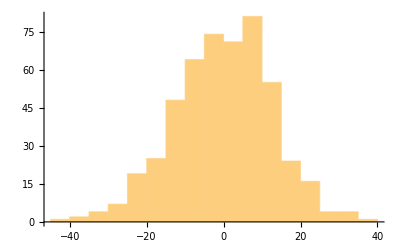

```mathematica
ClearAll[residuals,allResiduals];
residuals[t_,n_/;1≤n≤Ns]:=
partialsFn[Μ,bts⟦1⟧].ξcol[t,n]-ζcol[t];

(allResiduals=Fold[conjColumns,residuals[0,#]&/@Range[Ns]])//MatrixForm
Mean[allResiduals]//Length
Histogram[Mean[allResiduals]]
```

New Weights

What is the probability of each particle ξ given its corresponding Ν observations ζ?

```mathematica
PDF[NormalDistribution[μ,σ]]
```

Function[x,(ⅇ^(-(x-μ)^2/(2 σ^2)))/(√(2 π) σ)]

#### pres [ particle-number ]

Assume that residuals have zero theoretical mean. The Ν data points from the evaluation of the polynomial over the Ν points of the Bishop training set amount to a sample of size Ν of the distribution of residuals. The chances of observing a particular residual are roughly:

```mathematica
ClearAll[pres];(* probability of a particular sample of the distribution of residuals *)
pres[ρn_]:=
With[{var=scalar@Variance[ρn],x=scalar@Mean[ρn],μ=0},
1/(√(2.π var))Exp[-(x-μ)^2/(2var)]];
```

According to Lesly María Acosta Argueta, from equation 2.41 on page 28 of Particle Filtering Estimation for Linear and Nonlinear
State-Space Models, the new weights should be multiplied (pointwise) by the old weights.

{4.74492×10^-20,0.00155558,0.00550331,0.0000555393,0.00325057,0.00307589,«489»,0.0012855,0.000626035,0.000175876,0.00293171,0.000206422}

1.

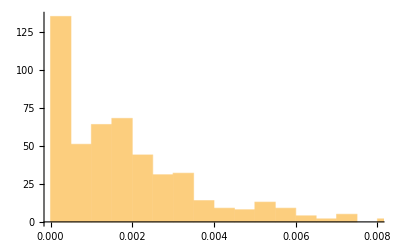

```mathematica
ws[1]=
With[{ps=MapThread[Times,{ws[0],pres[residuals[0,#]]&/@Range[Ns]}]},
With[{s=Plus@@ps},
ps/s]];
ws[1]//Short[#,3]&
Plus@@ws[1]
Histogram[ws[1]]
```

Examine the new weights:

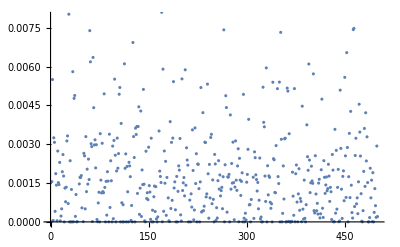

```mathematica
ListPlot[ws[1]]
```

Cull Particles

Keep only the particles that “do well” for the next time step, by some criterion driven by hyperparameters.

Pair each particle with its index:

```mathematica
ClearAll[indexedWeights$];
(indexedWeights$=MapThread[List,{Range[Ns],ws[1]}])//Short
```

{{1,4.74492×10^-20},{2,0.00155558},«496»,{499,0.00293171},{500,0.000206422}}

Keep the top fraction p for a total of p N_s survivors. Later, copy and perturb each survivor 1/p times to get a new population of size N_s.

```mathematica
ClearAll[sortedIndexedWeights$,topPWeights$,topPIndexedWeights$,topPIndices$,topPParticles$];
<|"sortedIndexedWeights"->((sortedIndexedWeights$=Reverse@SortBy[indexedWeights$,Last])//Short),
"topPIndexedWeights"->((topPIndexedWeights$=sortedIndexedWeights$⟦;;Floor[p Ns]⟧)//Short),
"topPWeights"->((topPWeights$=Last/@topPIndexedWeights$)//Short),
"topPIndices"->((topPIndices$=First/@topPIndexedWeights$)//Short),
"topPParticles//Dims"->((topPParticles$=(ξs[0]⟦All,#⟧&/@topPIndices$)ᵀ)//Dimensions),
"top 3 Particles"->(topPParticles$⟦All,1;;3⟧//MatrixForm)|>
```

<|sortedIndexedWeights→{{179,0.0282564},{165,0.0170997},«496»,{33,4.56668×10^-56},{390,3.53505×10^-84}},topPIndexedWeights→{{179,0.0282564},{165,0.0170997},«46»,{268,0.00487676},{36,0.00477421}},topPWeights→{0.0282564,0.0170997,0.0161285,«45»,0.00487676,0.00477421},topPIndices→{179,165,43,42,346,309,308,212,49,170,28,464,463,265,60,«20»,325,106,230,362,373,347,142,443,363,82,105,295,37,268,36},topPParticles//Dims→{10,50},top 3 Particles→(0.907564 | 3.46283 | -2.64094
-3.7429 | -3.17967 | 9.5657
-1.16238 | -9.99931 | -5.54584
4.56636 | -1.3058 | 4.87202
-6.07017 | 3.42279 | -3.85583
10.4265 | 7.85658 | -21.4438
-9.78013 | 4.14237 | 14.2841
0.0232982 | -0.190005 | -4.44097
14.7645 | 4.22444 | 20.607
-8.33096 | -10.2815 | -9.32722)|>

Structure can emerge after culling:

```mathematica
threeDPointClouds[topPParticles$,σ0]
```

Top p Particles

Replace each particle with 1/p copies, each perturbed by a new σ_1.

### Standard Deviations

Particles are still in the columns.

```mathematica
topPParticles$//Dimensions
```

{10,50}

Each standard deviation pertains to each of the Μ+1 components of a particle. Each component will be independently sampled.

The following is an improper column vector, that is, a one-dimensional list.

```mathematica
ClearAll[σξ];
σξ[1]=StandardDeviation/@topPParticles$
```

{3.40383,9.42767,9.72726,11.7887,8.08174,8.98597,7.44684,10.3517,10.2938,9.29819}

### Unbiased Importance Sample

#### resampled [ ξ, σ_ξ, how-many-copies ]

```mathematica
ClearAll[resampled];
resampled[ξ_,σξ_,copyCount_]:=
Table[
RandomVariate[
NormalDistribution[
ξ⟦m,1⟧,
σξ⟦m,1⟧],
copyCount],
{m,Μ+1}];
(* Just look at the fourth particle from the top. *)
resampled[List/@topPParticles$⟦All,4⟧,List/@σξ[1],3]//Dimensions
```

{10,3}

New Particle Cloud

```mathematica
topPParticles$//Dimensions
```

{10,50}

```mathematica
topPParticles$ᵀ⟦1⟧
```

{0.907564,-3.7429,-1.16238,4.56636,-6.07017,10.4265,-9.78013,0.0232982,14.7645,-8.33096}

```mathematica
(ξs[1]=Fold[
conjColumns,
Map[(* same as /@ *)
Function[improperColumn,
resampled[
List/@improperColumn,
List/@σξ[1],
Floor[1/p]]],
Transpose[topPParticles$]]])//Dimensions
```

{10,500}

Examine for structure:

```mathematica
threeDPointClouds[ξs[1],σ0]
```

We will need to fudge the standard deviations (another ad-hoc procedure amongst several in particle-filtering). Some standard deviations go down, others go up. We will fudge by exponentially reducing the standard deviations each round.

```mathematica
Dimensions@ξs[1]
```

{10,500}

Remember, StandardDeviation is column-wise so we must map it over the Μ+1 rows of each population of size N_s of particles. This usage produces an improper column vector.

```mathematica
StandardDeviation/@ξs[0]
```

{10.0268,9.24812,9.48964,10.5916,10.5584,9.61175,9.53736,9.88231,10.5015,9.98443}

```mathematica
StandardDeviation/@ξs[1]
```

{5.09767,13.1719,14.0307,16.9403,11.3127,12.1243,10.4433,15.0487,14.8632,13.0051}

Package and Experiment

Abstract the procedures above and iterate.

Three .7fkludges:

Exponentially attenuate the standard deviations

Add a regularization parameter, λ, to penalize particles of large norm.

Multiply new weights by old weights (not actually a kludge, but a procedure of proven optimality; see Argueta’s thesis op. cit.)

We have some global variables, namely Μ and N_s. Assert that input dimensions match expectations w.r.t. these globals.

Add a regularization parameter, λ, to penalize particles of large norm.

We employ lambda-lifting to implement ambient monads over constants from the training set and hyperparameters.

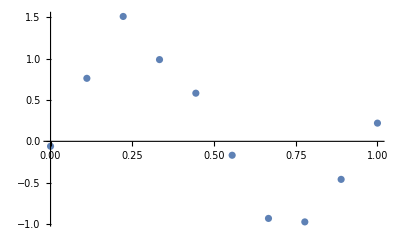
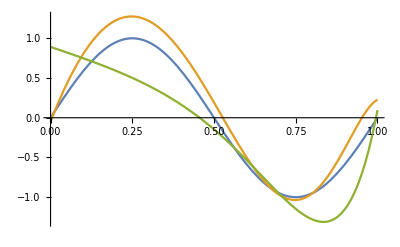
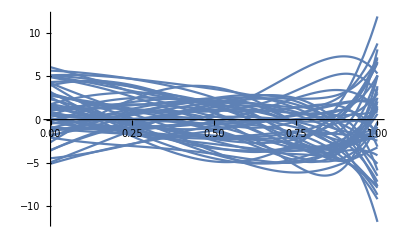
<|Mean/@topp→{0.891519,-1.39446,-0.0970227,-2.12684,-0.0149176,-0.429161,-7.29871,9.74732,0.0669173,0.750542},bts→-Graphics-,kalman→-Graphics-,ptcl→-Graphics-,Dims@cts→{2},Dims/@cts→{{50},{10,50}},Dims@weightsImproperCol→{500},Dims@topPWeightsAndParticles→{2},Dims@ws[0]→{500},Dims@ξs[0]→{10,500},Dims@iteratedWeights→{500},Dims@iteratedParticles→{10,500},Dims@folded→{2},Short[fts]→{{0.0135768,0.0135768,0.0135768,0.0135768,0.0135768,0.0135768,«489»,0.00369259,0.00369259,0.00369259,0.00369259,0.00369259},{{«1»},«8»,{«1»}}},Short[its]→{{0.0243384,0.0243384,0.0243384,0.0243384,0.0243384,0.0243384,«488»,0.00478311,0.00478311,0.00478311,0.00478311,0.00478311,0.00478311},«1»}|>

```mathematica
ClearAll[regula,prFn,weightsImproperCol,indexedWeights,sortedIndexedWeights,topPIndexedWeights,topPIndices,topPWeightsAndParticles,culled,iterated];
On[Assert];

regula[λ_][ξ_]:=(λ(ξ.ξ));

prFn[A_,ζ_][ξ_]:=pres[ζ-A.ξ];

weightsImproperCol[xs_,ζ_,λ_][wsIn_,ξs_]:=
With[{A=partialsFn[Μ,xs]},
With[{cost=(regula[λ]/@(ξsᵀ))+1/(prFn[A,ζ]/@(ξsᵀ))},
With[{wpre=MapThread[Times,{wsIn,cost}]},
1/wpre/Plus@@(1/wpre)]]];

indexedWeights[wsImp_]:=MapThread[List,{Range[Ns],wsImp}];

sortedIndexedWeights[wsImp_]:=Reverse@SortBy[indexedWeights[wsImp],Last];

topPIndexedWeights[p_,wsImp_]:=sortedIndexedWeights[wsImp]⟦;;Floor[p Ns]⟧;

topPIndices[p_,wsImp_]:=First/@topPIndexedWeights[p,wsImp];

topPWeightsAndParticles[p_,wsImp_,ξsIn_]:=
With[{topIndices=topPIndices[p,wsImp]},
{wsImp⟦#⟧&/@topIndices,Transpose[ξsIn⟦All,#⟧&/@topIndices]}];

culled[xs_,ζ_,λ_,p_  ][{wsIn_,ξs_}]:=
With[{wts=weightsImproperCol[xs,ζ,λ][wsIn,ξs]},
topPWeightsAndParticles[p,wts,ξs]];

iterated[xs_,ζ_,λ_,p_,σfudge_][{wsIn_,ξs_}]:=
Module[{culledWeights,culledParticles},
{culledWeights,culledParticles}=culled[xs,ζ,λ,p][{wsIn,ξs}];
With[{σξ=List/@(σfudge*StandardDeviation/@culledParticles)},
With[{resultingParticles=Fold[
conjColumns,
resampled[List/@#,σξ,Floor[1/p]]&/@Transpose[culledParticles]],
resultingWeights=Flatten[ConstantArray[#,Floor[1/p]]&/@culledWeights]},
Assert[{Μ+1,Ns}===Dimensions[resultingParticles]];
Assert[{Ns}===Dimensions[resultingWeights]];
{resultingWeights,resultingParticles}]]];

With[{λ=10.^-3,xs=bts⟦1⟧,ζ=List/@bts⟦2⟧,σfudge=0.5},
With[{
wts=weightsImproperCol[xs,ζ,λ][ws[0],ξs[0]],its=iterated[xs,ζ,λ,p,σfudge][{ws[0],ξs[0]}],
fts=Fold[
iterated[xs,ζ,λ,p,σfudge][#1]&,(* ignore #2 *)
{ws[0],ξs[0]},
Range[32]]},
With[{cts=culled[xs,ζ,λ,0.1][fts],terms=symbolicPowers[x,Μ]},
With[{topp=cts⟦2⟧},
<|"Mean/@topp"->Mean/@topp,
"bts"->ListPlot[btsᵀ],
"kalman"->Plot[{Sin[2π x],{terms}.goodSolution,terms.(Mean/@topp)},{x,0,1}],
"ptcl"->Plot[terms.topp,{x,0,1}],
"Dims@cts"->Dimensions@cts,
"Dims/@cts"->Dimensions/@cts,
(* "cts"->MatrixForm/@cts, *)
"Dims@weightsImproperCol"->Dimensions @ wts,
"Dims@topPWeightsAndParticles"->Dimensions[topPWeightsAndParticles[wts,ξs[0]]],
"Dims@ws[0]"->Dimensions@ws[0],
"Dims@ξs[0]"->Dimensions@ξs[0],
"Dims@iteratedWeights"->Dimensions@First@its,
"Dims@iteratedParticles"->Dimensions@Last@its,
"Dims@folded"->Dimensions@fts,
"Short[fts]"->Short[fts,3],
"Short[its]"->Short[its,3]|>]]]]
```

```mathematica
ClearAll[looseThreeDPointClouds];
looseThreeDPointClouds[ξs_]:=
DynamicModule[{i=1,j=2,k=3},
Manipulate[Graphics3D[Point/@({ξs⟦i,All⟧,ξs⟦j,All⟧,ξs⟦k,All⟧}ᵀ),
Axes->True,AspectRatio->1,
AxesLabel->{"i: "<>ToString[i],"j: "<>ToString[j],"k: "<>ToString[k]}],
Grid[{
{"i",SetterBar[Dynamic[i],Range[Μ+1]]},
{"j",SetterBar[Dynamic[j],Range[Μ+1]]},
{"k",SetterBar[Dynamic[k],Range[Μ+1]]}}]]];
```

```mathematica
With[{xs=bts⟦1⟧,ζ=List/@bts⟦2⟧,σfudge=0.5},
Manipulate[
Module[{topWeights,topParticles,top,topσ},
{topWeights,topParticles}=
culled[xs,ζ,10.0^log10λ,0.01][
Fold[
iterated[xs,ζ,10.0^log10λ,p,σfudge][#1]&,(* ignore #2 *)
{ws[0],ξs[0]},
Range[2^log2ℐ]]];
top=Mean/@topParticles;
topσ=StandardDeviation/@topParticles;
Grid[{
{Module[{x},
With[{terms=symbolicPowers[x,Μ]},
With[{lp=ListPlot[btsᵀ,
PlotMarkers->{Graphics@{Blue,Circle[{0,0},1]},.05}]},
Module[{showlist={lp,Plot[Sin[2.π x],{x,0,1},PlotStyle->{Thick,Green}]}},
AppendTo[showlist,Plot[{terms}.goodSolution,{x,0,1},PlotStyle->{Purple}]];
AppendTo[showlist,Plot[terms.top,{x,0,1},PlotStyle->{Red}]];
Show[showlist,Frame->True,ImageSize->Medium,FrameLabel->{{"z",""},{"x",""}}]]]]],
Column[{
ListLinePlot[{top,Flatten[goodSolution]}],
ListLinePlot[topσ]}]
}
}]],
Grid[{{Button["RESET",(log10λ=-3.0;log2ℐ=5)&],
Control[{{log10λ,-2.50,"log_10λ"},-6.0,3.0,0.10,Appearance->{"Open","Labeled"}}]},
{Button["NOP",(log10λ=1.0log10λ+0.0000001)&],
Control[{{log2ℐ,5,"log_2ℐ"},0,10,1,Appearance->{"Open","Labeled"}}]}   }]]]
```

## Conclusion